# Integrals For Dummies

## If we can, you can!

Progetto d’esame: Matematica Computazionale & Calcolo Numerico e Software Didattico.

```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

-Graphics- -Graphics- -Graphics- -Graphics-

Autori:

Tommaso Saracchini  | Domenico Coriale | Giuseppe De Palma | Eduart Uzeir

Per iniziare ad usare questa applicazione ed imparare tutto ciò che serve sugli integrali, devi premere il pulsante START. Buon divertimento!

Button[-Graphics-,SetDirectory[NotebookDirectory[]];<<"Package.m`";ButtonData→NotebookLocate["Index"];]

-Graphics-

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

# Indice

## Primo Livello:

```mathematica
Print[Framed[Hyperlink["Integrali Definiti", {"Project.nb","DefiniteTheory"}],FrameStyle->Directive[Orange,12], Background->LightBlue]]
```

Integrali DefinitiProject.nbDefiniteTheoryProject.nb

"Integrali Definiti"Project.nbDefiniteTheoryProject.nb

```mathematica
Print[Framed[Hyperlink["Integrali Indefiniti", {"Project.nb","IndefiniteTheory"}],FrameStyle->Directive[Orange,12],Background->LightBlue]]
```

Integrali IndefinitiProject.nbIndefiniteTheoryProject.nb

"Integrali Indefiniti"Project.nbIndefiniteTheoryProject.nb

## Secondo Livello:

```mathematica
Print[Framed[Hyperlink["Teorema Fondamentale", {"Project.nb","TeoremaFondamentale"}],FrameStyle->Directive[Orange,12], Background->LightBlue]]
```

Teorema FondamentaleProject.nbTeoremaFondamentaleProject.nb

"Teorema Fondamentale"Project.nbTeoremaFondamentaleProject.nb

```mathematica
Print[Framed[Hyperlink["Metodi di Risoluzione degli Integrali", {"Project.nb","Metodi"}],FrameStyle->Directive[Orange,12], Background->LightBlue]]
```

Metodi di Risoluzione degli IntegraliProject.nbMetodiProject.nb

"Metodi di Risoluzione degli Integrali"Project.nbMetodiProject.nb

## Allenamento:

Esercizi su Integrali Definiti

Esercizi su Integrali Indefiniti

Esercizi Personalizzabili

### Second level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

#### Third level section heading

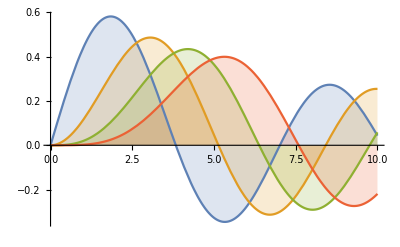

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

# Integrali Definiti

Che cosa sono gli integrali definiti? E soprattutto: a cosa servono?
In Matematica, cosi` come in Fisica, puo` capitare di dover calcolare l’area sottostante ad una curva descritta da una funzione, gli integrali ci permettono di fare proprio questo.
Prendiamo una funzione, come ad esempio quella nell’immagine di sotto, e due punti a e b sull’asse delle x che sono gli estremi dell’intervallo al quale siamo interessati.
Ci chiediamo: come facciamo a calcolare l’area tra la curva , l’asse delle ‘x’ e i due segmenti verticali x=a e x=b?
Per farlo ci servono gli integrali!

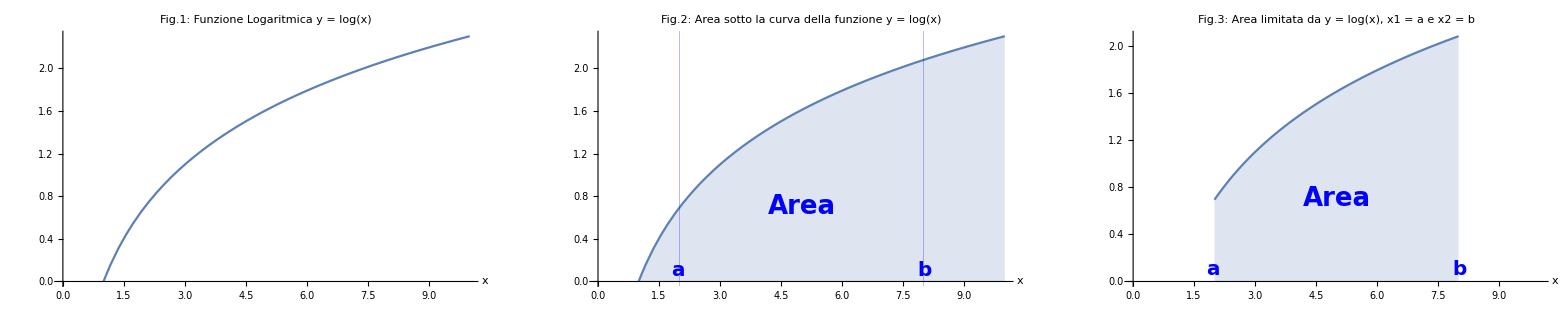

```mathematica
(* definisco i tre punti di rifferimento ossia sinistra, centro e desta*)
align[Right] = {1, 0};
align[Center] = {0, 0}; 
align[Left] = {-1, 0};
(* definisco lo stile del testo che voglio scrivere *)
lText = Text[Style["a", Blue, Bold, FontSize->20], {1.8, 0.1}, align[Left]];
cText = Text[Style["Area", Blue, Bold, Underlined, FontSize->26], {5.0, 0.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {8.2, 0.1}, align[Right]];

txt = Graphics[{lText, cText, rText}];
f[x_]:=Log[x]
(* costruisco i grafi in tre passi diversi *)
plot0=Plot[f[x], {x, 1, 10}, AxesOrigin->{0,0},PlotLabel->Style[Framed["Fig.1: Funzione Logaritmica y =" Log[x]], 22, Bold, Blue, Background->Lighter[Pink]], AxesLabel->Automatic];
plot0; (* la funzione logaritmica nel intervalo [0, 10]*)
plot1=Plot[f[x], {x, 1, 10}, AxesOrigin->{0,0}, Filling->Axis, PlotLabel->Style[Framed["Fig.2: Area sotto la curva della funzione y =" Log[x]], 22, Bold, Blue, Background->Lighter[Pink]], 
GridLines->{{{2, Blue}, {8, Blue}}, None}, PlotRange -> {{0, 10}, All}, AxesLabel->Automatic];
Show[plot1, txt];(* la funzione e i punti x=a e x=b *)
plot2=Plot[f[x], {x, 2, 8}, AxesOrigin->{0,0}, Filling->Axis, PlotLabel->Style[Framed["Fig.3: Area limitata da y = log(x), x1 = a e x2 = b"], 22, Bold, Blue, Background->Lighter[Pink]], 
(*GridLines->{{{2, Blue}, {8, Blue}}, None}*) PlotRange -> {{0, 10}, All}, AxesLabel->Automatic];
(* l'area che vogliamo calcolare *)
GraphicsRow[{plot0, Show[plot1, txt], Show[plot2,txt]}]
```

```mathematica
Framed[Button[-Graphics-, ButtonData->NotebookLocate["Index"];] Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite1"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

## Andiamo per passi: Area del rettangolo

Prendiamo una funzione semplice (la funzione costante), cioè una retta parallela all’asse delle ‘x’ (ad esempio la retta di equazione f(x) = 4).
Siamo interessati a calcolare l’area sotto la funzione nell’intervallo di estremi a = 1 e b = 3 come in figura. 
Come facciamo?

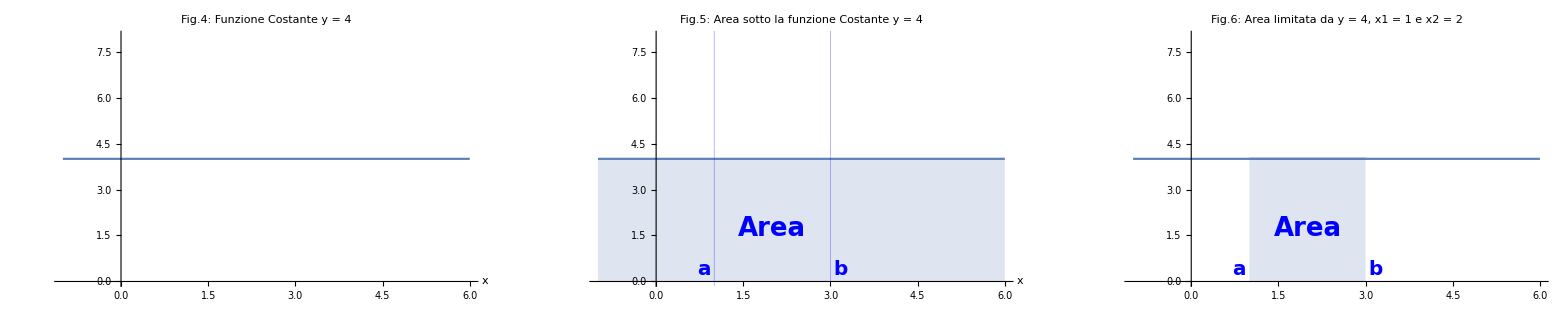

```mathematica
lText = Text[Style["a", Blue, Bold, FontSize->20], {0.7, 0.4}, align[Left]];
cText = Text[Style["Area", Blue, Bold, Underlined, FontSize->26], {2.0, 1.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {3.3, 0.4}, align[Right]];

txt2 = Graphics[{lText, cText, rText}];
funlim1 = -1;
funlim2 = 6;
f[x_]:=4
plot3=Plot[f[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.4: Funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic];
plot4=Plot[y=4, {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.5: Area sotto la funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], Filling->Axis, GridLines->{{{1, Blue}, {3, Blue}}, None},
AxesOrigin->{0,0}, AxesLabel->Automatic];
(*Plot[y=4, {x, 1, 3}, PlotLabel->Style[Framed["Fig.4: Funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], Filling->Axis, GridLines->{{{1, Blue}, {3, Blue}}, None}, 
AxesOrigin->{0,0}, AxesLabel->Automatic]*)
inlimit1 = 1;
inlimit2 = 3;
(*f[x_] = 100 - 8*x^2 + x^3;*)
g1 = Plot[f[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.6: Area limitata da y = 4, x1 = 1 e x2 = 2"], 22, Bold, Blue, Background->Lighter[Pink]]];
g2 = Plot[f[x], {x, inlimit1, inlimit2}, 
   Filling -> 0];
GraphicsRow[{plot3, Show[plot4, txt2], Show[g1, g2, txt2]}]
```

Semplice : è un rettangolo!!! Sapendo che il rettangolo dato ha base 2 ed altezza 4 l'area sara’ 8.
Quindi diciamo che l'integrale da 1 a 3 della funzione f (x) = 4 in dx e' uguale a 8! Facile no?! 

In simboli:

```mathematica
<<MaTeX`
MaTeX[HoldForm[Integrate[f[x],{x,1,3}] = 8], Magnification->3]
```

-Graphics-

Ti stai chiedendo cosè dx? Lo scopriamo tra poco...! Intanto facciamo un altro semplice esempio.

```mathematica
Print[Framed["Informazioni supplementari sul" Hyperlink[RETTANGOLO, "http://mathworld.wolfram.com/Rectangle.html"]]]
```

Informazioni supplementari sul [RETTANGOLO](http://mathworld.wolfram.com/Rectangle.html)

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["DefiniteTheory"];]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];] Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Andiamo per passi: Area del trapezio

Prendiamo come funzione una qualunque retta inclinata, ad esempio f(x) = x + 1. 
Come facciamo a calcolare l’area nell’intervallo di estremi a = 1 e b = 4?

Questa volta abbiamo di fronte un trapezio. Qui possiamo ancora arrangiarci con la geometria tradizionale.
Conoscendo la formula per calcolare l’area del trapezio arriviamo a dire che:

```mathematica
MaTeX[HoldForm[A = Integrate[f[x], {x, 1,5}] = 16], Magnification->3]
```

-Graphics-

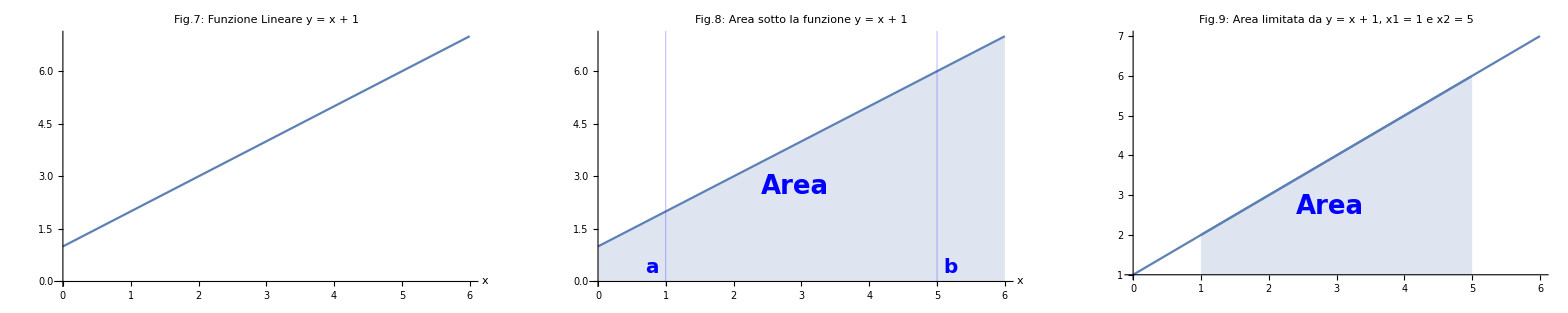

```mathematica
lText = Text[Style["a", Blue, Bold, FontSize->20], {0.7, 0.4}, align[Left]];
cText = Text[Style["Area", Blue, Bold, Underlined, FontSize->26], {2.9, 2.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {5.3, 0.4}, align[Right]];

txt2 = Graphics[{lText, cText, rText}];
funlim1 = 0;
funlim2 = 6;
f1[x_]:=x+1
plot3=Plot[f1[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.7: Funzione Lineare y = x + 1"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic];
plot4=Plot[f1[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.8: Area sotto la funzione y = x + 1"], 22, Bold, Blue, Background->Lighter[Pink]], Filling->Axis, GridLines->{{{1, Blue}, {5, Blue}}, None},
AxesOrigin->{0,0}, AxesLabel->Automatic];
(*Plot[y=4, {x, 1, 3}, PlotLabel->Style[Framed["Fig.4: Funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], Filling->Axis, GridLines->{{{1, Blue}, {3, Blue}}, None}, 
AxesOrigin->{0,0}, AxesLabel->Automatic]*)
inlimit1 = 1;
inlimit2 = 5;
(*f[x_] = 100 - 8*x^2 + x^3;*)
g1 = Plot[f1[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.9: Area limitata da y = x + 1, x1 = 1 e x2 = 5"], 22, Bold, Blue, Background->Lighter[Pink]]];
g2 = Plot[f1[x], {x, inlimit1, inlimit2}, 
   Filling -> 1.0];
GraphicsRow[{plot3, Show[plot4, txt2], Show[g1, g2, txt2]}]
```

```mathematica
Print[Framed["Informazioni supplementari sul" Hyperlink[TRAPEZIO, "http://mathworld.wolfram.com/Trapezoid.html"]]]
```

Informazioni supplementari sul [TRAPEZIO](http://mathworld.wolfram.com/Trapezoid.html)

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Definite1"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite3"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Andiamo per passi: Area delle Curve

Ma se volessimo calcolare l’area sotto delle funzioni curve, come questa per esempio:

```mathematica
<<MaTeX`
MaTeX[HoldForm[f[x]=e^x], Magnification->3]
```

-Graphics-

Oppure

```mathematica
<<MaTeX`
MaTeX[HoldForm[f[x] = x^3 - 8x^2 + 100], Magnification->3]
```

-Graphics-

In questo caso la geometria tradizionale non puo’ aiutarci... per fortuna ci sono gli integrali definiti.
Arriviamo quindi alla loro definizione:

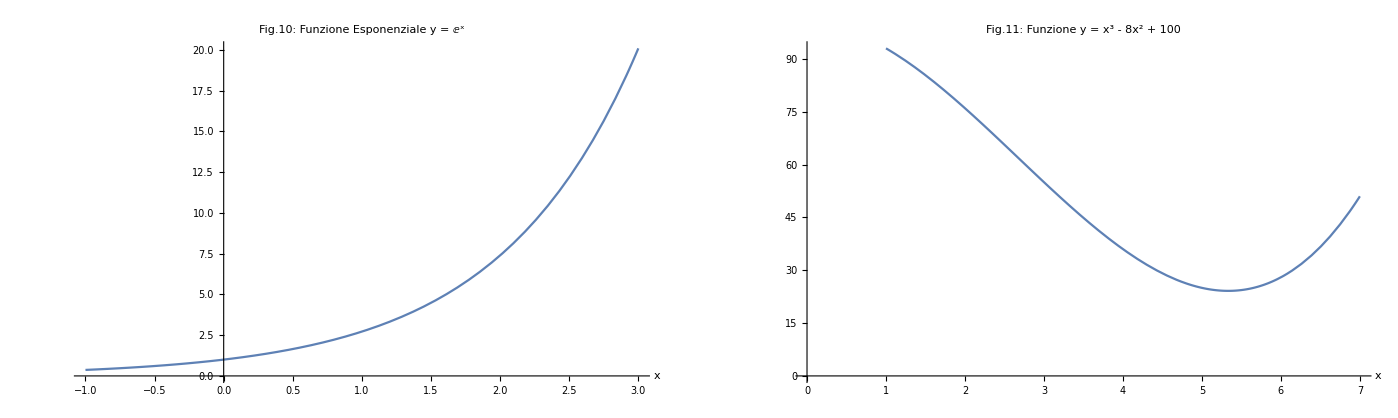

```mathematica
f2[x_]:= ⅇ^x;
f3[x_]:= 100-8*x^2+x^3;
funlim3 = -1;
funlim4 = 3;
funl1=1;
funl2=7;
plot5=Plot[f2[x], {x, funlim3, funlim4}, PlotLabel->Style[Framed["Fig.10: Funzione Esponenziale y = ⅇ^x"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic];
plot6=Plot[f3[x], {x, funl1, funl2}, PlotLabel->Style[Framed["Fig.11: Funzione y = x^3 - 8x^2 + 100"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic];

GraphicsRow[{plot5, plot6}]
```

```mathematica
<<MaTeX`
Style[Grid[{{"Abbiamo incontrato nelle slide precedenti la scrittura",MaTeX[HoldForm[Integrate[f[x], {x,a,b}]], Magnification->3],", ma cosa vogliamo dire con questi simboli?"}}],FontFamily->"Nimbus Sans L", FontSize->26]
```

Abbiamo incontrato nelle slide precedenti la scrittura | -Graphics- | , ma cosa vogliamo dire con questi simboli?

⟶  ∫  sta per “somma” di cosa? Lo vedremo tra poco;

⟶ a e b sono gli estremi dell’intervallo di integrazione, cioè la “base” dell’area che vogliamo calcolare;

⟶ f(x) è la funzione che conosciamo;

⟶ dx rappresenta anche lui una “base”, ma quale base?

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Definite2"];]Button[-Graphics-, ButtonData->NotebookLocate["Index"];] Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite4"]; ], 
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Definizioni

Possiamo pensare di dividere l’intervallo [a, b] in 4 intervalli uguali. Tracciamo dei segmenti verticali in modo da costruire dei rettangoli che non oltrepassano la funzione, come in figura.

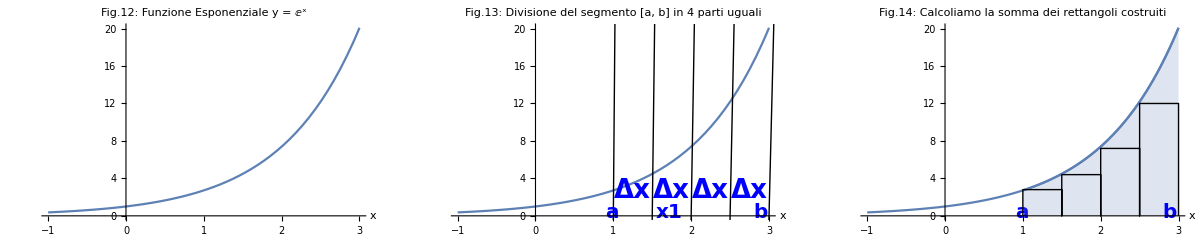

```mathematica
lText = Text[Style["a", Blue, Bold, FontSize->20], {0.9, 0.4}, align[Left]];
lTextt = Text[Style["x1", Blue, Bold, FontSize->20], {1.55, 0.4}, align[Left]];
cText = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {1.25, 2.7}, align[Center]];
cText2 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {1.75, 2.7}, align[Center]];
cText3 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {2.25, 2.7}, align[Center]];
cText4 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {2.75, 2.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {2.98, 0.4}, align[Right]];

lText1 = Text[Style["a", Blue, Bold, FontSize->20], {0.9, 0.4}, align[Left]];
cText1 = Text[Style["", Blue, Bold, Underlined, FontSize->26], {2.9, 2.7}, align[Center]];
rText1 = Text[Style["b", Blue, Bold, FontSize->20], {2.97, 0.4}, align[Right]];

txt3 = Graphics[{lText,lTextt, cText, cText2,cText3,cText4, rText}];

txt4 = Graphics[{lText1, cText1, rText1}];

plott=Plot[f2[x], {x, -1, 3}, PlotLabel->Style[Framed["Fig.12: Funzione Esponenziale y = ⅇ^x"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic]; (**)
plott0=Plot[f2[x], {x, -1, 3}, PlotLabel->Style[Framed["Fig.13: Divisione del segmento [a, b] in 4 parti uguali"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic,
Epilog->{
InfiniteLine[{1, 0}, {1, 1000}], 
InfiniteLine[{1.5, 0}, {1.5, 1000}],
InfiniteLine[{2, 0}, {2, 1000}],
InfiniteLine[{2.5, 0}, {2.5, 1000}],
InfiniteLine[{3, 0}, {3, 1000}]}];
plott1=Plot[f2[x], {x, -1, 3}, PlotLabel->Style[Framed["Fig.14: Calcoliamo la somma dei rettangoli costruiti"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic,
Epilog->{Line[{{1, 0}, {1, 2.8}, {1.5, 2.8}, {1.5, 0}, {1.5, 4.4}, {2, 4.4}, {2, 0}, {2, 7.2}, {2.5, 7.2}, {2.5, 0}, {2.5, 12}, {3, 12}, {3, 0}}]}];
g2 = Plot[f2[x], {x, 1, 3}, 
   Filling -> 0];
GraphicsRow[{plott,Show[plott0, txt3], Show[plott1, g2, txt4]}]
```

Abbiamo quindi quattro rettangoli con la stessa base dx, ognuno con altezza diversa, ad esempio il primo ha altezza f(a), il secondo f(x1) e cosi via ... fino all’ultimo f(x3).
Chiamo S4 la somma delle aree dei quattro rettangoli che ne sono usciti.
Osserviamo che se sommiamo le aree di questi 4 rettangoli otteniamo un’area minore dell’area A sottesa alla curva (indicata con il color blu in figura 14) , 
cioè abbiamo che S4 < A. 
Possiamo fare meglio?!

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Definite3"];]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite5"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Definizione

Come possiamo ridurre l’errore tra la misura dell’area che abbiamo calcolato e la misura dell’area “vera”?
Possiamo dividere ulteriormente l’intervallo! Ad esempio in 10 intervalli uguali.

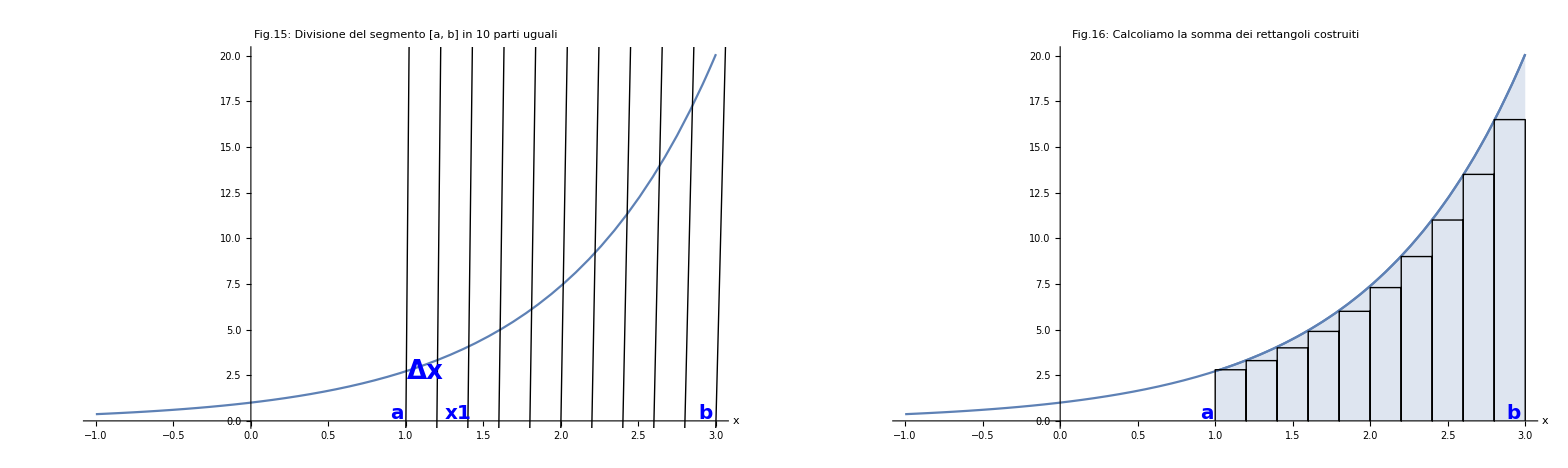

```mathematica
lText = Text[Style["a", Blue, Bold, FontSize->20], {0.9, 0.4}, align[Left]];
lTextt = Text[Style["x1", Blue, Bold, FontSize->20], {1.55, 0.4}, align[Left]];
lTexttA = Text[Style["x1", Blue, Bold, FontSize->20], {1.25, 0.4}, align[Left]];
cText = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {1.25, 2.7}, align[Center]];
cTextA = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {1.125, 2.7}, align[Center]];
cText2 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {1.75, 2.7}, align[Center]];
cText3 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {2.25, 2.7}, align[Center]];
cText4 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {2.75, 2.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {2.98, 0.4}, align[Right]];

lText1 = Text[Style["a", Blue, Bold, FontSize->20], {0.9, 0.4}, align[Left]];
cText1 = Text[Style["", Blue, Bold, Underlined, FontSize->26], {2.9, 2.7}, align[Center]];
rText1 = Text[Style["b", Blue, Bold, FontSize->20], {2.97, 0.4}, align[Right]];

txt3 = Graphics[{lText, lTexttA, cTextA, rText}];

txt4 = Graphics[{lText1, cText1, rText1}];
plott0=Plot[f2[x], {x, -1, 3}, PlotLabel->Style[Framed["Fig.15: Divisione del segmento [a, b] in 10 parti uguali"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic,
Epilog->{
InfiniteLine[{1, 0}, {1, 1000}],
InfiniteLine[{1.2, 0}, {1.2, 1000}], 
InfiniteLine[{1.4, 0}, {1.4, 1000}],
InfiniteLine[{1.6, 0}, {1.6, 1000}],
InfiniteLine[{1.8, 0}, {1.8, 1000}],
InfiniteLine[{2, 0}, {2, 1000}],
InfiniteLine[{2.2, 0}, {2.2, 1000}],
InfiniteLine[{2.4, 0}, {2.4, 1000}],
InfiniteLine[{2.6, 0}, {2.6, 1000}],
InfiniteLine[{2.8, 0}, {2.8, 1000}],
InfiniteLine[{3, 0}, {3, 1000}]}];
plott1=Plot[f2[x], {x, -1, 3}, PlotLabel->Style[Framed["Fig.16: Calcoliamo la somma dei rettangoli costruiti"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic,
Epilog->{Line[{{1, 0}, {1, 2.8}, {1.2, 2.8}, {1.2, 0}, {1.2, 3.3}, {1.4, 3.3}, {1.4, 0}, {1.4, 4}, {1.6, 4}, {1.6, 0}, {1.6, 4.9}, {1.8, 4.9}, {1.8, 0}, {1.8, 6}, {2, 6}, {2, 0}, 
{2, 7.3}, {2.2, 7.3}, {2.2, 0}, {2.2, 9}, {2.4, 9}, {2.4, 0}, {2.4, 11}, {2.6, 11}, {2.6, 0}, {2.6, 13.5}, {2.8, 13.5}, {2.8, 0}, {2.8, 16.5}, {3, 16.5}, {3, 0}}]}];
g2 = Plot[f2[x], {x, 1, 3}, 
   Filling -> 0];
GraphicsRow[{Show[plott0, txt3], Show[plott1, g2, txt4]}]
```

Abbiamo però lo stesso problema, possiamo notare dalla figura che la somma dell’area nei 10 rettangoli, cioè S10 è ancora minore dell’area A sottesa alla curva.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Definite4"];]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];] Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite6"]; ], 
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Definizione

In generale se dividessimo l’intervallo [a, b] in N intervalli avremmo che la somma delle aree degli N rettangoli, sara’ sempre minore dell’area che vogliamo calcolare, 
cioe’ SN < A per ogni N numero di intervalli.
Osserviamo dalla figura che, al crescere di N, i rettangoli diventano sempre piu’ piccoli e la differenza tra SN e A è sempre minore.
Prendiamo per esempio la funzione:

```mathematica
<<MaTeX`
MaTeX[HoldForm[f[x] = e ^x], Magnification->3]
```

-Graphics-

```mathematica
f[x_]:= ⅇ^x
plotChart[nrettangoli_] := Module[{}, low = 0; high = 2;
delta = (high - low)/nrettangoli;
colsum = Graphics[{FaceForm[{Opacity[0.7]}], Table[{Hue[1, 0.6, 0.8], EdgeForm[Thin], Rectangle[{low + n * delta, 0}, {low + (n + 1) * delta, f[low + n * delta]}]}, {n, 1, nrettangoli}]}, ImageSize->500, AspectRatio->1];
curve=Plot[f[x], {x, low, high}, PlotStyle->Thick, ImageSize->60];];
Manipulate[plotChart[nrettangoli];
Show[{colsum, curve}], {{nrettangoli,4}, 2, 80}]
```

Show::gcomb: Could not combine the graphics objects in Show[{colsum,curve}].

```mathematica
<<MaTeX`
Style[Grid[{{"Non ci resta altro da fare che \"mandare N all'infinito\", e cioè calcolare", MaTeX["\\lim_{N ->\\infty}S_N", Magnification->3], "."}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Non ci resta altro da fare che "mandare N all'infinito", e cioè calcolare | -Graphics- | .

Il risultato che ne salterà fuori sarà proprio l'area che stavamo cercando!

	    Quindi, ricapitoliamo: l'area che vogliamo calcolare è:

```mathematica
<<MaTeX`
MaTeX["A=\\int_{a}^{b} f(x)\,dx", Magnification->3]
```

-Graphics-

ovvero, 
⟶ la somma ∫
⟶ nell’intervallo [a, b] di rettangoli
⟶ di base dx
⟶ e altezza f(x)

```mathematica
Print[Framed["Informazioni supplementari sui" Hyperlink[LIMITI, "http://mathworld.wolfram.com/Limit.html"]]]
```

Informazioni supplementari sui [LIMITI](http://mathworld.wolfram.com/Limit.html)

```mathematica
Framed[
Button[ 
ImageRotate[-Graphics-],ButtonData->NotebookLocate["Definite5"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Framed[Hyperlink["Integrali\nIndefiniti", {"Project.nb","IndefiniteTheory"}],FrameStyle->Directive[Orange,12],Background->LightBlue],
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

-Graphics- -Graphics- Integrali
IndefinitiProject.nbIndefiniteTheoryProject.nb

# Integrali Indefiniti

Prima di spiegare che cosa è l’integrale indefinito, dobbiamo fare qualche premessa.
Partiamo dalla definizione di primitiva di una funzione: 
Sia f : [a, b]→ℝ, una funzione continua. Una funzione F(x) derivabile nell’intervallo [a, b] e’ una primitiva (o antiderivata) della funzione f se:

```mathematica
<<MaTeX`
Style[Grid[{{MaTeX["F'(x) = f(x)", Magnification->3], "per ogni",MaTeX["x \\in [a,b]", Magnification->3]}}], FontFamily->"Nimbus Sans L", Italic, FontSize->28]
```

-Graphics- | per ogni | -Graphics-

In altre parole una primitiva di una funzione f(x) non è altro che una funzione che una volta derivata dia proprio f(x).

## Esempio 1

```mathematica
<<MaTeX`
Style[Grid[{{"Se" ,MaTeX[HoldForm[f[x]=2 x], Magnification->3],"allora una sua primitiva è",MaTeX[HoldForm[F[x]=x^2], Magnification->3], "perché la derivata di ", MaTeX[HoldForm[x^2], Magnification->3], "è", MaTeX[HoldForm[2 x], Magnification->3], ", infatti", MaTeX["(x^2)' = 2x", Magnification->3] }}], FontSize->26, FontFamily->"Nimbus Sans L"]
```

Se | -Graphics- | allora una sua primitiva è | -Graphics- | perché la derivata di  | -Graphics- | è | -Graphics- | , infatti | -Graphics-

## Esempio 2

```mathematica
<<MaTeX`
Style[Grid[{{"Se" ,MaTeX[HoldForm[f[x]=Cos[x]], Magnification->3],"allora una sua primitiva è",MaTeX[HoldForm[F[x]=Sin[x]], Magnification->3], "perché la derivata di ", MaTeX[HoldForm[Sin[x]], Magnification->3], "è", MaTeX[HoldForm[Cos[x]], Magnification->3], ", infatti", MaTeX["(\\cos{x})' = \\sin{x}", Magnification->3] }}], FontSize->26, FontFamily->"Nimbus Sans L"]
```

Se | -Graphics- | allora una sua primitiva è | -Graphics- | perché la derivata di  | -Graphics- | è | -Graphics- | , infatti | -Graphics-

```mathematica
Print[Framed["Informazioni supplementari sui" Hyperlink[DERIVATI, "http://mathworld.wolfram.com/Derivative.html"]]]
```

Informazioni supplementari sui [DERIVATI](http://mathworld.wolfram.com/Derivative.html)

```mathematica
Framed[
Framed[Hyperlink["Integrali\nDefiniti", {"Project.nb","DefiniteTheory"}],FrameStyle->Directive[Orange,12], Background->LightBlue] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Indefinite1"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->400, Alignment->Baseline]
```

-Graphics- -Graphics- Integrali
DefinitiProject.nbDefiniteTheoryProject.nb

## Ancora primitive...

Possiamo fare un osservazione:
Avete notato che nella definizione c’è scritto “una primitiva” e non “la primitiva”?

```mathematica
<<MaTeX`
Style[Grid[{{"Riprendendo la funzione:", MaTeX["f(x) = 2x", Magnification->3]}}], FontSize->26, FontFamily->"Nimbus Sans L"]
```

Riprendendo la funzione: | -Graphics-

```mathematica
<<MaTeX`
Style[Grid[{{"Possiamo osservare anche che", MaTeX["F(x) = x^2 + 1", Magnification->3], "è anch'essa una primitiva di",MaTeX["f(x)", Magnification->3],  "infatti", MaTeX[ "(x^2 + 1)' = 2x", Magnification->3]}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Possiamo osservare anche che | -Graphics- | è anch'essa una primitiva di | -Graphics- | infatti | -Graphics-

Abbiamo trovato due primitive di una stessa funzione! Ma quante ce ne saranno?

Basti pensare che, tornando all'esempio precedente, potevamo aggiungere alla primitiva F(x) una costante qualsiasi dato che la derivata di una costante vale zero.
Infatti possiamo scrivere:

```mathematica
<<MaTeX`
MaTeX["(x^2 + C)' = (x^2)' + C' = 2x", Magnification->3]
```

-Graphics-

Percio' vediamo che se una funzione f(x) ammette primitiva F(x), allora ne ha  infinite che differiscono tutte da F(x) di una costante additiva ( C ).

A questo punto sapendo che se una funzione ammette una primitiva, ne ammette infinite, ha quindi senso definire l'insieme 
di tutte le primitive di una funzione e di attribuirgli un nome: 

lo chiameremo integrale indefinito di una funzione.

## Definizione

Sia f(x) una funzione, si chiama integrale indefinito di f(x) l’insieme di tutte le primitive della funzione f(x) e si indica con il simbolo:

```mathematica
<<MaTeX`
MaTeX[HoldForm[Integrate[f[x], x]], Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
Style[Grid[{{"In base a quanto detto sulle primitive possiamo dire che:", MaTeX[HoldForm[Integrate[f[x], x]=F[x] + C], Magnification->3], "dove", MaTeX["F(x)", Magnification->3], "è una primitiva di", MaTeX["f(x)", Magnification->3]}}], FontSize->26, FontFamily->"Nimbus Sans L"]
```

In base a quanto detto sulle primitive possiamo dire che: | -Graphics- | dove | -Graphics- | è una primitiva di | -Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["IndefiniteTheory"];]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];] Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Indefinite2"]; ], 
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Nota bene!

Anche se la notazione non lo lascia intendere esplicitamente sottolineiamo che l’integrale indefinito identifica un insieme di funzioni
e non una funzione in particolare.
Questo fatto viene messo in evidenza dalla costante additiva C, che è arbitraria e non deve essere omessa.
Facciamo qualche semplice esempio per chiarire le idee:

```mathematica
<<MaTeX`
Style[Grid[{
{"1.", MaTeX[HoldForm[Integrate[x,x] = x^2/2 + C], Magnification->3], "          2.", MaTeX[HoldForm[Integrate[e^x,x] = e^x + C], Magnification->3] },
{"3.", MaTeX[HoldForm[Integrate[1/x, x] = Log[|x|] + C], Magnification->3], "          4.", 
MaTeX[HoldForm[Integrate[1/x^2, x] = -1/x + C], Magnification->3] },
{"5.", MaTeX[HoldForm[Integrate[x^2,x] = x^3/3 + C], Magnification->3]}
}], FontFamily->"Nimbus Sans L", FontSize->28, Italic]
```

1. | -Graphics- |           2. | -Graphics-
3. | -Graphics- |           4. | -Graphics-
5. | -Graphics- |  |

per C costante qualsiasi.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Indefinite1"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Framed[Hyperlink["Teorema\nFondamentale", {"Project.nb","TeoremaFondamentale"}],FrameStyle->Directive[Orange,12], Background->LightBlue], 
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->450, Alignment->Baseline]
```

-Graphics- -Graphics- Teorema
FondamentaleProject.nbTeoremaFondamentaleProject.nb

# Teorema Fondamentale

Quello che vediamo ora è che la notazione utilizzata per gli integrali definiti e indefiniti è molto simile... perchè?
 
Le definizioni che abbiamo dato ad entrambe sono completamente diverse.
L’integrale definito di una funzione in un certo intervallo indica un’area e cioè un numero.
L’integrale indefinito di una funzione e’ invece un insieme di funzioni, che non ha nulla a che vedere con il concetto di area.
Ma allora perchè le loro notazioni sono cosi simili? La risposta la troviamo nel seguente teorema.

## Teorema fondamentale del calcolo integrale

Sia f:[a, b]→ℝ una funzione e sia G(x) una sua primitiva. Allora:

```mathematica
<<MaTeX`
MaTeX[HoldForm[Integrate[f[x], {x,a,b}] = "[G(x)]_a^b" =G[b] - G[a]], Magnification->3]
```

-Graphics-

Questo teorema fondamentale stabilisce un legame tra l'integrale definito e l'integrale indefinito, il quale non era per niente ovvio dalle sole definizioni date ad entrambi!

In particolare, ci permette di risolvere integrali definiti usando il concetto di primitiva di una funzione, e cioè con gli integrali indefiniti.
Ecco svelato il perchè delle notazioni molto simili, ma andiamo subito a calcolare il nostro primo integrale.

```mathematica
Print[Framed["Informazioni supplementari sul" Hyperlink[TEOREMA FONDAMENTALE DEL CALCOLO INTEGRALE, "http://mathworld.wolfram.com/FundamentalTheoremsofCalculus.html"]]]
```

Informazioni supplementari sul [CALCOLO DEL FONDAMENTALE INTEGRALE TEOREMA](http://mathworld.wolfram.com/FundamentalTheoremsofCalculus.html)

```mathematica
Framed[
Framed[Hyperlink["Integrali\nIndefiniti", {"Project.nb","IndefiniteTheory"}],FrameStyle->Directive[Orange,12],Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Teorema1"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

-Graphics- -Graphics- Integrali
IndefinitiProject.nbIndefiniteTheoryProject.nb

## Il mio primo integrale

Vogliamo calcolare l’area sottesa alla curva di funzione f(x)=x^2 nell’intervallo [1, 2]

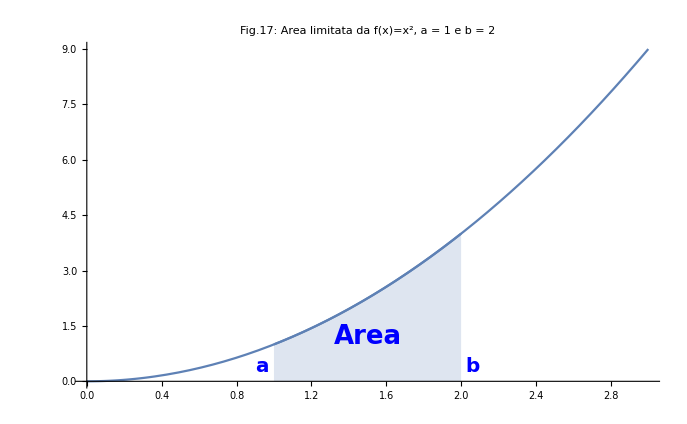

```mathematica
leftText = Text[Style["a", Blue, Bold, FontSize->20], {0.9, 0.4}, align[Left]];
centerText = Text[Style["Area", Blue, Bold, FontSize->26], {1.5, 1.2}, align[Center]];
rightText = Text[Style["b", Blue, Bold, FontSize->20], {2.1, 0.4}, align[Right]];
txt5 = Graphics[{leftText, centerText, rightText}];

fu[x_]:=x^2;
go1 = Plot[fu[x], {x, 0, 3}, PlotLabel->Style[Framed["Fig.17: Area limitata da f(x)=x^2, a = 1 e b = 2"], 22, Bold, Blue, Background->Lighter[Pink]]];
go2 = Plot[fu[x], {x, 1, 2}, 
   Filling -> 0];
Show[go1, go2, txt5]
```

```mathematica
<<MaTeX`
Style[Grid[{{ "Quindi possiamo calcolare l'area A con la seguente formula:", MaTeX[HoldForm[A = Integrate[x^2, {x, 0,1}]], Magnification->3]}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Quindi possiamo calcolare l'area A con la seguente formula: | -Graphics-

```mathematica
<<MaTeX`
Style[Grid[{{ "Il teorema precedente mi dice che devo trovare una primitiva della funzione", MaTeX[HoldForm[f[x] = x^2], Magnification->3]}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Il teorema precedente mi dice che devo trovare una primitiva della funzione | -Graphics-

```mathematica
<<MaTeX`
Style[Grid[{{ "Ricordandosi le regole di derivazione dei polinomi, non dovrebbe risultare difficile trovare:", MaTeX[HoldForm[G[x] = x^3/3+C], Magnification->3]}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Ricordandosi le regole di derivazione dei polinomi, non dovrebbe risultare difficile trovare: | -Graphics-

Trucco:

Notate che, mi basta conoscere una sola primitiva di f(x), e quindi per semplicità posso prendere la primitiva con la costante C = 0!
Una volta trovata G(x) vado ad applicare il teorema:

```mathematica
<<MaTeX`
MaTeX[HoldForm[A =Integrate[x^2, {x,1,2}] = G[2] - G[1] = 2^3/3 - 1^3/3 = 8/3 - 1/3 = 7/3], Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["TeoremaFondamentale"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Teorema2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Il mio primo integrale

Osservate che se avessimo preso una qualunque altra primitiva G(x) = x^3/3 + C, con C un numero qualsiasi,
avremmo avuto lo stesso risultato.

```mathematica
<<MaTeX`
MaTeX[HoldForm[A =Integrate[x^2, {x,1,2}] = G[2] - G[1] = (2^3/3 + C) - (1^3/3 + C) = 8/3 + C - 1/3 -C = 7/3], Magnification->3]
```

-Graphics-

Questo perche, in questo procedimento, le costanti si eliminano a vicenda.

Vediamo un'altro esempio.
Calcolare l'area sotto alla funzione coseno tra - π/2 e π/2.

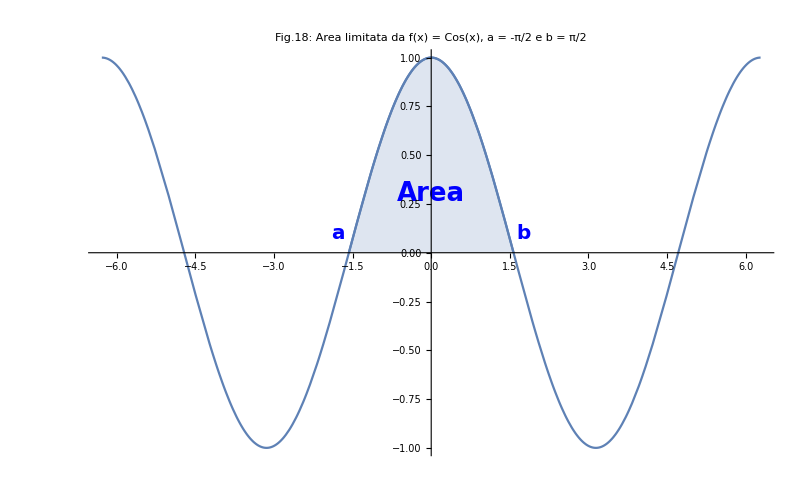

```mathematica
leftText1 = Text[Style["a", Blue, Bold, FontSize->20], {- 1.9, 0.1}, align[Left]];
centerText1 = Text[Style["Area", Blue, Bold, FontSize->26], {0, 0.3}, align[Center]];
rightText1 = Text[Style["b", Blue, Bold, FontSize->20], {1.9, 0.1}, align[Right]];
txt6 = Graphics[{leftText1, centerText1, rightText1}];

fu1[x_]:=Cos[x];
go11 = Plot[fu1[x], {x, -2π, 2π}, PlotLabel->Style[Framed["Fig.18: Area limitata da f(x) = Cos(x), a = -π/2 e b = π/2"], 22, Bold, Blue, Background->Lighter[Pink]]];
go22 = Plot[fu1[x], {x, -π/2, π/2}, 
   Filling -> 0];
   Show[go11, go22, txt6]
```

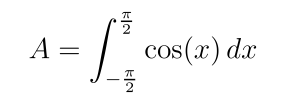
L'area sarà data dalla formula | -Graphics-

```mathematica
<<MaTeX`
Style[Grid[{{"L'area sarà data dalla formula", MaTeX[HoldForm[A= Integrate[Cos[x], {x, -Pi/2, Pi/2}]],Magnification->3]}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Troviamo una primitiva, G(x) = sin(x), la prendiamo con costante C = 0 per l'osservazione precedente e abbiamo:

```mathematica
<<MaTeX`
MaTeX[HoldForm[A = Integrate[Cos[x], {x, -Pi/2, Pi/2}] = G[Pi/2] - G[-Pi/2] = Sin[Pi/2] - Sin[-Pi/2] = 1 - (-1) = 2], Magnification->3]
```

-Graphics-

```mathematica
Print[Framed["Informazioni supplementari sulle" Hyperlink[FUNZIONI TRIGONOMETRICHE, "http://mathworld.wolfram.com/TrigonometricFunctions.html"]]]
```

Informazioni supplementari sulle [FUNZIONI TRIGONOMETRICHE](http://mathworld.wolfram.com/TrigonometricFunctions.html)

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Teorema1"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Framed[Hyperlink["Metodi di Risoluzione\ndegli Integrali", {"Project.nb","Metodi"}],FrameStyle->Directive[Orange,12], Background->LightBlue], 
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->580, Alignment->Baseline]
```

-Graphics- -Graphics- Metodi di Risoluzione
degli IntegraliProject.nbMetodiProject.nb

# Metodi di Integrazione

In questa lezione imparerai dei metodi di integrazione per i definiti e indefiniti (clicca sui links!):

## Indefiniti:

Integrali Fondamentali

Per Scomposizione

Per Sostituzione

Per Parti

Razionali

```mathematica
Framed[
Button[ImageResize[-Graphics-, 80], ButtonData->NotebookLocate["Index"];],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->150, Alignment->Baseline]
```

-Graphics-

# Integrali Fondamentali

Risolvere un integrale indefinito di una funzione significa trovare una primitiva. ( Vai alla Teoria )
Con questa “guida all’integrazione” riuscirai senz’altro a risolvere il tuo integrale indefinito.

Le regole di derivazione studiate suggeriscono dei modi per trovare una primitiva di una funzione. Andiamo quindi a vedere i vari   metodi che, pur non essendo un procedimento generale, permettono comunque di trovare una primitiva delle funzioni più comuni.

Gli integrali fondamentali sono gli integrali “notevoli” che ogni studente che affronta l’argomento deve conoscere.
La definizione stessa di integrale indefinito ci suggerisce come fare per risolverli. Infatti dato che

```mathematica
<<MaTeX`
MaTeX["f(x) = kx$ allora $f(x)' = k$ con $k \\in R", Magnification->3]
```

-Graphics-

abbiamo la regola, cioè

```mathematica
<<MaTeX`
MaTeX[HoldForm[Integrate[k, x] = k x + C], Magnification->3]
```

-Graphics-

Allo stesso modo, seguono tutte le altre formule principali di integrazione “immediata”:

```mathematica
<<MaTeX`
MaTeX["\\int k \,dx =kx +C", Magnification->3]
MaTeX["\\int x^n\,dx=\\frac{x^{n+1}}{n+1}+C \\quad n \\ne 1", Magnification->3]
MaTeX["\\int \\frac{1}{x} \,dx= \\log |x| + C", Magnification->3]
MaTeX["\\int \\sin x \,dx= -\\cos x + C", Magnification->3]
MaTeX["\\int \\cos x \,dx= \\sin x + C", Magnification->3]
MaTeX["\\int e^x \,dx=e^x+C", Magnification->3]
MaTeX["\\int \\frac{1}{\\cos^2 x}\,dx= \\tan x + C", Magnification->3]
MaTeX["\\int \\frac{1}{\\sin^2 x}\,dx=\\cot x + C", Magnification->3]
MaTeX["\\int \\frac{1}{1+x^2} \,dx= \\arctan x + C", Magnification->3]
```

-Graphics-

-Graphics-

-Graphics-

«6 more identical outputs»

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Framed[
Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Framed[Hyperlink["Scomposizione\nIndefiniti", {"Project.nb","MetodiIndScomposizione"}],
FrameStyle->Directive[Orange,12], Background->LightBlue],
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->460, Alignment->Baseline]
```

-Graphics- -Graphics- Scomposizione
IndefinitiProject.nbMetodiIndScomposizioneProject.nb

# Scomposizione

L’integrale indefinito ha due proprietà utili a semplificare il loro calcolo:

Prima proprietà di linearità:

L’integrale della somma di funzioni è uguale alla somma degli integrali delle singole funzioni.

```mathematica
<<MaTeX`
MaTeX["\\int  \\left[ f(x)+g(x) \\right] \, dx=\\int f(x)\, dx+\\int g(x)\, dx", Magnification->3]
```

-Graphics-

(* Link su perche succede questo*)

Seconda proprietà di linearità:

L’integrale del prodotto di una funzione per una costante è uguale al prodotto tra la costante e l’integrale della funzione.

```mathematica
<<MaTeX`
MaTeX["\\int kf(x)\, dx=k\\int f(x)\, dx", Magnification->3]
```

-Graphics-

(* Link su perche succede questo*)

Esercizio:
Trovare una primitiva della funzione

```mathematica
<<MaTeX`
MaTeX["f(x)=3e^x+2x^2-\\frac{1}{2}\\cos x", Magnification->3]
```

-Graphics-

```mathematica
PopupWindow[Button[ Style["Soluzione Guidata", Large]], "Mostriamo passo passo la soluzione:" PopupWindow[Button["Annida"], "annidato"] , WindowTitle->"Soluzione", WindowFloating->True, WindowMovable->True]
```

Soluzione Guidata

```mathematica
Framed[
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Framed[Hyperlink["Sostituzione\nIndefiniti", {"Project.nb","MetodiIndefinitiSostituzione"}],
FrameStyle->Directive[Orange,12], Background->LightBlue],
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->560, Alignment->Baseline]
```

-Graphics- Sostituzione
IndefinitiProject.nbMetodiIndefinitiSostituzioneProject.nb Torna ai MetodiProject.nbMetodiProject.nb

# Sostituzione

## Teoria 1

Come integrare funzioni del tipo	 f(ϕ(x)) ϕ’(x)?

IIl nostro scopo è quello di semplificare l’integrale con un’opportuna sostituzione della variabile x ! 
La seguente formula è chiamata prima formula di sostituzione (*Link sul perchè succede questo*)

```mathematica
<<MaTeX`
MaTeX["\\int f(\\phi(x))\\phi'(x)\,dx=\\int f(t) \,dt", Magnification->3]
```

-Graphics-

Questa formula esprime come si trasforma l’espressione dell’integrale passando dalla variabile di integrazione x alla nuova variabile t = ϕ(x). L’operazione
da compiere si può ricordare così: oltre a scrivere t al posto di ϕ(x) si deve sostituire formalmente ϕ’(x) dx con dt,

```mathematica
<<MaTeX`
MaTeX["t = \\phi(x)$ allora $\\phi' dx = dt", Magnification->3]
```

-Graphics-

Se F’(t) = f cioè se si conosce una primitiva di f, l’integrale di destra è uguale a F(t) + C e, per trovare la primitiva della funzione di partenza f(ϕ(x)) ϕ’(x) basta sostituire
al posto di t la funzione ϕ(x).

```mathematica
<<MaTeX`
MaTeX["\\int f(\\underbrace{\\phi(x)}_{t})\\underbrace{\\phi'(x)\,dx}_{dt}=\\int f(t) \,dt=F(\\underbrace{t}_{\\phi(x)})+C=F(\\phi(x)) +C", Magnification->3]
```

-Graphics-

La domanda naturale è: come individuare una decomposizione della funzione integranda del tipo? Un metodo generale non c'e: occorre esercizio, esperienza
ed anche una certa dose di fortuna... Più si sperimenta e più si impara ad accorgersi delle funzioni che si integrano in questo modo.

```mathematica
Framed[
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndProcedimento"]; ],
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- Torna ai MetodiProject.nbMetodiProject.nb

## Procedimento - Esempio 1

Un esempio vale più di mille parole:

```mathematica
<<MaTeX`
MaTeX["\\int \\sin (x^2)  2x \,dx", Magnification->3]
```

-Graphics-

Vediamo che l'integrale è riconducibile alla prima formula di integrazione per sostituzione! Infatti:

-Graphics-

-Graphics-

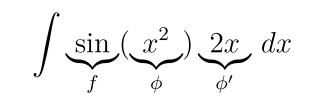
-Graphics-
-Graphics-

```mathematica
<<MaTeX`
MaTeX["\\int\\underbrace{ \\sin }_{f} (\\underbrace{x^2}_{\\phi}) \\underbrace{2x}_{\\phi'}\,dx", Magnification->3]
MaTeX["f(\\phi(x))=sin(x^2) \\quad \\Longrightarrow \\quad\\phi (x)=x^2=t \\quad \\Longrightarrow \\quad\\phi'(x)=2x", Magnification->3]
```

```mathematica
<<MaTeX`
Text["Quindi ci basta porre" MaTeX["t=\\phi (x)=x^2$ e $dt=\\phi'(x)dx=2x dx \\quad", Magnification->3], BaseStyle->{28, "Nimbus Sans L"}]
```

Quindi ci basta porre -Graphics-

E vediamo che cosa succede all’integrale:

```mathematica
<<MaTeX`
MaTeX["\\int \\sin(\\underbrace{x^2}_{t})  \\underbrace{2x \,dx}_{dt}= \\int sin (t) \,dt", Magnification->3]
```

-Graphics-

2) Si è semplificato notevolmente! Dalla tabella degli integrali fondamentali sappiamo trovare una primitiva. Quindi:

```mathematica
PopupWindow[Button[Style["Vedi la tabella!", Large]], -Graphics-]
```

Vedi la tabella!

```mathematica
<<MaTeX`
MaTeX["\\int \\sin (t) \,dx=-\\cos(t) + C", Magnification->3]
```

-Graphics-

3) Ora non dimentichiamoci di ritornare alla variabile interessata cioè la x, quindi:

```mathematica
<<MaTeX`
MaTeX["-\\cos (\\underbrace{t}_{x^2}) + C=-\\cos (x^2)+C", Magnification->3]
```

-Graphics-

Perciò:

```mathematica
<<MaTeX`
MaTeX["\\int \\sin(x^2)  2x \,dx=-\\cos (x^2)+C", Magnification->3]
```

-Graphics-

Con questa formula appena trovata possiamo inoltre ampliare la tabella degli integrali fondamentali in questo modo. Vediamolo con un esempio!

## Procedimento - Esempio 2

Supponiamo di voler trovare una primitiva della generica funzione

```mathematica
<<MaTeX`
MaTeX["f(x)=\\frac{\\phi'(x)}{\\phi(x)} \\quad  \\quad con\\phi(x) derivabile", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
Text["Ponendo" MaTeX["t=\\phi(x)$ e $dt=\\phi'(x)dx", Magnification->3], BaseStyle->{28, "Nimbus Sans L"}]
```

Ponendo -Graphics-

Andiamo a risolvere l’integrale:

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{\\phi'(x)}{\\phi(x)}\,dx=\\int \\frac{1}{t} \,dt=\\ln(|t|)+C=\\ln(|\\phi(x)|)+C", Magnification->3]
```

-Graphics-

Con una sostituzione ci siamo ricondotti ad un integrale fondamentale! Possiamo ripetere il procedimento con tutti gli integrali nella tabella e quindi formare 
una nuova tabella più generale:

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndefinitiSostituzione"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndSostituzione2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- Torna ai MetodiProject.nbMetodiProject.nb

## Teoria 2

Spesso ci si trova a lavorare con espressioni della forma:

```mathematica
<<MaTeX`
MaTeX["\\int f(\\phi (x)) \, dx", Magnification->3]
```

-Graphics-

dove nell’integrale abbiamo una funzione composta f(ϕ(x)), senza il fattore moltiplicativo ϕ’(x). 

E’ possibile applicare la sostituzione t = ϕ(x) ?


Se la funzione ϕ(x) è invertibile tutto fila liscio. Sia ψ la funzione inversa di ϕ

```mathematica
<<MaTeX`
MaTeX["\\psi ^{-1}:=\\phi", Magnification->3]
```

-Graphics-

Allora con il cambio di variabile t = ϕ(x) avrò che

```mathematica
<<MaTeX`
MaTeX["t=\\phi(x)\\quad \\Longrightarrow\\quad   \\psi(t)= x \\quad \\Longrightarrow\\quad \\psi'(t)dt=dx", Magnification->3]
```

-Graphics-

Dunque l’integrale si trasforma ottenendo una formula generale chiamata seconda formula di sostituzione:

```mathematica
<<MaTeX`
MaTeX["\\int f(\\phi (x)) \, dx=\\int f(t)\\psi'(t) \,dt", Magnification->3]
```

-Graphics-

## Esempio

Calcolare

```mathematica
<<MaTeX`
MaTeX["\\int (1+e^x)^2 \,dx", Magnification->3]
```

-Graphics-

L’integrale è riconducibile alla seconda formula di sostituzione! Infatti:

```mathematica
<<MaTeX`
MaTeX["\\int \\overbrace{(\\underbrace{1+e^x}_{\\phi(x)})^2}^{f(\\phi(x))} \,dx", Magnification->3]
```

-Graphics-

Riconosciamo che la sostituzione opportuna è la seguente

```mathematica
<<MaTeX`
MaTeX["\\phi(x)=1+e^x=t \\quad \\Longrightarrow\\quad f(\\phi(x))=f(t)=t^2", Magnification->3]
```

-Graphics-

1) Quindi ci basta porre

```mathematica
<<MaTeX`
MaTeX["t=\\phi(x)=1+e^x", Magnification->3]
```

-Graphics-

Poi trovare

```mathematica
<<MaTeX`
MaTeX["x=\\psi(t)=\\ln(x-1)", Magnification->3]
```

-Graphics-

e porre

```mathematica
<<MaTeX`
MaTeX["dx=\\psi'(t)dt=\\frac{1}{t-1}dt", Magnification->3]
```

-Graphics-

E l’integrale diventa:

```mathematica
<<MaTeX`
MaTeX["\\int (1+e^x)^2 \,dx=\\int \\underbrace{t^2}_{f} \\underbrace{\\frac{1}{t-1}\,dt}_{dx} =\\int \\frac{t^2}{t-1} \,dt", Magnification->3]
```

-Graphics-

2) Eseguendo la divisione tra polinomi ho che

```mathematica
<<MaTeX`
MaTeX["\\frac{t^2}{t-1}=t+1+\\frac{1}{t-1}", Magnification->3]
```

-Graphics-

E quindi:

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{t^2}{t-1} \,dt=\\int t+1+\\frac{1}{t-1}\,dt=\\frac{1}{2}t^2+t+\\ln(t-1)+C", Magnification->3]
```

-Graphics-

3) Ora non dimentichiamoci di tornare alla variabile di partenza, quindi

```mathematica
<<MaTeX`
MaTeX["\\frac{1}{2}t^2+t+\\ln(t-1)+C=\\frac{1}{2}(\\underbrace{1+e^x}_{t})^2+\\underbrace{1+e^x}_{t}+\\ln(\\underbrace{1+e^x}_{t}-1)+C", Magnification->3]
```

-Graphics-

Perciò:

```mathematica
<<MaTeX`
MaTeX["\\int (1+e^x)^2 \,dx=\\frac{1}{2}e^{2x}+2e^x+x+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndProcedimento"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Framed[Hyperlink["Per Parti\nIndefiniti", {"Project.nb","MetodiIndParti"}],
FrameStyle->Directive[Orange,12], Background->LightBlue],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

-Graphics- -Graphics- Per Parti
IndefinitiProject.nbMetodiIndPartiProject.nb Torna ai MetodiProject.nbMetodiProject.nb

# Per Parti

Un altro metodo ampiamente usato per integrare e’ detto metodo di integrazione per parti, la formula e’ la seguente:

```mathematica
<<MaTeX`
MaTeX["\\int g'(x)f(x)\,dx=g(x)f(x)-\\int g(x)f'(x)\,dx", Magnification->3]
```

-Graphics-

(*Link su nuovo notebook sulla provenienza della formula*)
L’integrale della funzione g’(x)f(x) viente trasformato in una parte integrata, il termine g(x)f(x), sottraendo l’integrale della funzione g(x)f’(x).

Attenzione!

Il metodo e’ vantaggioso solo se per il termine g(x)f’(x) si conosce un metodo di integrazione!
Nelle prossime slide vedremo una classe di esempi di integrali risolvibili tramite la formula precedente.

```mathematica
Framed[
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndParti2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics- Torna ai MetodiProject.nbMetodiProject.nb

## Esempio 1 Prendiamo l’integrale della funzione, f(x)=x e^x

```mathematica
<<MaTeX`
MaTeX["\\int xe^x\,dx", Magnification->3]
```

-Graphics-

Con le notazioni precedenti vediamo che

```mathematica
<<MaTeX`
MaTeX["\\int xe^x\,dx=\\int \\underbrace{x}_{f}\\underbrace{e^x}_{g'}\,dx=\\underbrace{xe^x}_{fg}-\\int\\underbrace{e^x}_{gf'}\,dx=(x-1)e^x+C", Magnification->3]
```

-Graphics-

Anche nel caso della funzione x^2 e^x si puo’ procedere in modo analogo, iterando due volte l’applicazione della formula di integrazione per parti

```mathematica
<<MaTeX`
MaTeX["\\int x^2e^x\,dx=\\int\\underbrace{x^2}_{f}\\underbrace{e^x}_{g'}\,dx=x^2e^x-2\\int xe^x\,dx=x^2e^x-2((x-1)e^x+C)=(x^2-2x+2)e^x+C", Magnification->3]
```

-Graphics-

E’ chiaro a questo punto che e’ possibile, iterando n volte l’uso della formula, risolvendo integrali del tipo:

```mathematica
<<MaTeX`
MaTeX["\\int p(x)e^x\,dx\\quad p(x)\\ polinomio\\ di\\ grado\\ n", Magnification->3]
```

-Graphics-

In modo analogo e’ possibile calcolare anche integrali della forma:

```mathematica
<<MaTeX`
MaTeX["\\int p(x)e^{ax}\,dx \\quad a \\in \\Re", Magnification->3]
```

-Graphics-

Basta osservare che 1/a(e^ax)' =e^ax. Ad esempio:

```mathematica
<<MaTeX`
MaTeX["\\int x^2e^{3x} \,dx=\\frac{1}{3}x^2e^{3x}-\\frac{2}{3}\\int xe^{3x} \,dx=\\frac{1}{3}x^2e^{3x}-\\frac{2}{9}\\left( xe^{3x}- \\int e^{3x} \,dx \\right)=\\left( \\frac{1}{3}x^2-\\frac{2}{9}x+\\frac{2}{27} \\right)e^{3x}+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndParti"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndParti3"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- Torna ai MetodiProject.nbMetodiProject.nb

## Esempio 2 Allo stesso modo si calcolano

```mathematica
<<MaTeX`
MaTeX["\\int x\\sin (x)\,dx=-x\\cos(x)+\\int \\cos(x)\,dx=\\sin(x)-x\\cos(x)+C", Magnification->3]
Print["e"]
MaTeX["\\int x\\cos (x)\,dx=x\\sin(x)-\\int \\sin(x)\,dx=\\cos(x)+x\\sin(x)+C", Magnification->3]
```

-Graphics-

e

-Graphics-

-Graphics-
e
-Graphics-

In generale, iterando il procedimento un numero opportuno di volte si calcolano gli integrali:

```mathematica
<<MaTeX`
MaTeX["\\int p(x)\\sin(ax) \,dx \\quad e\\quad \\int p(x)\\cos(ax)\,dx \\quad \\quad a \\in \\Re", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndParti2"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndParti4"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- Torna ai MetodiProject.nbMetodiProject.nb

## Esempio 3 Sempre tramite l’integrazione per parti, si risolvono anche

```mathematica
<<MaTeX`
MaTeX["\\int p(x)\\ln(x)\,dx", Magnification->3]
```

-Graphics-

Proviamo a calcolare l’integrale di ln(x)

```mathematica
<<MaTeX`
MaTeX["\\int \\ln(x) \,dx=\\int \\underbrace{1}_{g'}\\cdot \\underbrace{\\ln(x)}_{f}\,dx=\\underbrace{x\\ln(x)}_{gf}-\\int \\underbrace{x}_{g}\\cdot\\underbrace{\\frac{1}{x}}_{f'} \,dx=x\\ln(x)-x+C", Magnification->3]
```

-Graphics-

Come abbiamo notato dall’ultimo esempio e’ comune utilizzare questi “trucchi” per utilizzare i metodi che conosciamo. 
Nel prossimo metodo vedremo un altro trucco comune per ricondurci a metodi che sappiamo usare.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndParti3"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Framed[Hyperlink["Funzioni Razionali\nIndefiniti", {"Project.nb","MetodiIndRazionali"}],
FrameStyle->Directive[Orange,12], Background->LightBlue],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->530, Alignment->Baseline]
```

-Graphics- -Graphics- Funzioni Razionali
IndefinitiProject.nbMetodiIndRazionaliProject.nb Torna ai MetodiProject.nbMetodiProject.nb

# Funzioni Razionali

Affrontiamo ora il problema di integrare funzioni razionali, cioe’ risolvere integrali del tipo

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{p(x)}{q(x)} \,dx \\quad p(x),q(x) \\quad polinomi ", Magnification->3]
```

-Graphics-

Anzitutto: se il grado del numeratore e’ >= del grado del denominatore, per prima cosa si esegue la divisione di polinomi; questo porta a riscrivere l’integranda come somma di un polinomio (che si integra immediatamente), piu’ una funzione razionale avente grado del numeratore minore del grado del denominatore.

## Esempio

```mathematica
<<MaTeX`
MaTeX["\\int\\frac{x^3+x}{x^2+x+1} \,dx", Magnification->3]
```

-Graphics-

la divisione di polinomi da’

```mathematica
<<MaTeX`
MaTeX["x^3+x=(x^2+x+1)(x-1)+(x+1)", Magnification->3]
```

-Graphics-

quindi

```mathematica
<<MaTeX`
MaTeX["\\int\\frac{x^3+x}{x^2+x+1} \,dx=\\int x-1 \,dx+\\int \\frac{x+1}{x^2+x+1} \,dx", Magnification->3]
```

-Graphics-

Fatta questa premessa possiamo quindi supporre che il grado del numeratore sia gia’ minore del grado del denominatore.
Andiamo ora ad enunciare i 3 possibili casi in cui puo’ apparire la nostra funzione razionale da integrare.

```mathematica
Framed[
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali1"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics- Torna ai MetodiProject.nbMetodiProject.nb

## Denominatore di 1° grado (e quindi per l’osservazione fatta il numeratore è una costante)

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{a}{bx+c}", Magnification->3]
```

-Graphics-

conservation è un integrale immediato, la formula generale si ricava facilmente

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{a}{bx+c}\,dx=\\frac{a}{b}\\ln(|bx+c|)+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- Torna ai MetodiProject.nbMetodiProject.nb

## Denomiantore di 2°grado con Δ < 0 In questo caso avremo un integrale del tipo:

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{p(x)}{ax^2+bx+c}\,dx", Magnification->3]
```

-Graphics-

Dove p(x) e’ un polinomio di grado 1 o 0 ed il denominatore ha discriminante associato ( Δ = b^2- 4ac) minore di zero.
Distinguiamo i due casi in base al grado del numeratore.

numeratore p(x) di grado 0

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{k}{ax^2+bx+c}\,dx", Magnification->3]
```

-Graphics-

Per calcolare l’integrale dobbiamo scrivere il denominatore come somma tra una costante ed un quadrato perfetto, in modo da ricondurci alla derivata 
di un’arcotangente.
Come farlo...? Semplice!
Basta raccogliere a fattor comune il coefficiente del termine x^2 (quindi “a” nella nostra notazione) per poi aggiungere e sottrarre b^2/(4 a^2). 
Vediamo subito un esempio.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali1"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali3"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- Torna ai MetodiProject.nbMetodiProject.nb

## Esempio

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{5}{2x^2+2x+1} \,dx", Magnification->3]
```

-Graphics-

Riconosciamo che il denominatore ha discriminante minore di zero e quindi procediamo come detto poco fa.

```mathematica
<<MaTeX`
MaTeX["2x^2+2x+1=2\\left( x^2+x+\\frac{1}{2} \\right)", Magnification->3]
```

-Graphics-

All’interno della coppia di parentesi tonde sommiamo e sottraiamo

```mathematica
<<MaTeX`
MaTeX["\\frac{b^2}{4a^2}=\\frac{1}{4}", Magnification->3]
```

-Graphics-

percio’

```mathematica
<<MaTeX`
MaTeX["2\\left( x^2+x+\\frac{1}{2} \\right)=2\\left( x^2+x+\\frac{1}{4}-\\frac{1}{4}+\\frac{1}{2} \\right) =2\\left[ \\left( x+\\frac{1}{2} \\right)^2+\\frac{1}{4} \\right]", Magnification->3]
```

-Graphics-

Proprio quello che volevamo, adiamo a metterlo nell’integrale, quindi

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{5}{2x^2+2x+1} \,dx=\\int \\frac{5}{2\\left[ \\left( x+\\frac{1}{2} \\right)^2+\\frac{1}{4} \\right]} \,dx=\\frac{5}{2}\\int \\frac{1}{ \\left( x+\\frac{1}{2} \\right)^2+\\frac{1}{4}} \,dx", Magnification->3]
```

-Graphics-

L’integrale cosi ottenuto ricorda il seguente integrale notevole

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{f'(x)}{(f(x))^2+1}\,dx=\\arctan(f(x))+C", Magnification->3]
```

-Graphics-

Facendo qualche altro piccolo conto algebrico

```mathematica
<<MaTeX`
MaTeX["\\frac{5}{2}\\int \\frac{1}{ \\left( x+\\frac{1}{2} \\right)^2+\\frac{1}{4}} \,dx=\\frac{5}{2}\\int \\frac{1}{\\frac{1}{4} \\left[ \\frac{\\left( x+\\frac{1}{2} \\right)^2}{\\frac{1}{4}}+1\\right]} \,dx=\\frac{5}{2}\\cdot4\\int \\frac{1}{4 \\left( x+\\frac{1}{2} \\right)^2+1} \,dx=", Magnification->3]
MaTeX["=10\\int \\frac{1}{4 \\left( \\frac{2x+1}{2} \\right)^2 +1} \,dx=5\\int \\frac{2}{(2x+1)^2+1}\,dx=5\\arctan(2x+1)+C", Magnification->3]
```

-Graphics-

-Graphics-

numeratore p(x) di grado 1, cioe’ del tipo

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{Ax+B}{ax^2+bx+c}\,dx", Magnification->3]
```

-Graphics-

Si riducono sempre alla somma tra un’arcotangente ed un logaritmo, ovvero

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{Ax}{ax^2+bx+c}\,dx+ \\int \\frac{B}{ax^2+bx+c}\,dx", Magnification->3]
```

-Graphics-

il secondo integrale sara’ del tipo trattato nel caso precedente, mentre il primo integrale sara’ della forma

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{f'(x)}{f(x)}\,dx=\\ln|f(x)|+C", Magnification->3]
```

-Graphics-

cioe’ dobbiamo andare a “costruire” al numeratore la derivata del denominatore.
Vediamolo con un esempio.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali2"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali4"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

## Esempio

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{4x}{x^2-x+1}\,dx", Magnification->3]
```

-Graphics-

La cosa da fare e’ quindi ottenere a numeratore la derivata del denominatore che e’

```mathematica
<<MaTeX`
MaTeX["\\frac{d}{dx}(x^2-x+1)=2x+1", Magnification->3]
```

-Graphics-

quindi portiamo fuori un 2 dal numeratore

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{4x}{x^2-x+1}\,dx=2\\int \\frac{2x}{x^2-x+1}\,dx", Magnification->3]
```

-Graphics-

Usiamo il trucco: sommiamo e sottraiamo 1

```mathematica
<<MaTeX`
ActionMenu[Text[Style["Trucco", Black, 28]], {Text[Style["Sommiamo e sottraiamo 1", Red, 28]] :> Print[MaTeX["\\int \\frac{4x}{x^2-x+1}\,dx=2\\int \\frac{2x}{x^2-x+1}\,dx=2\\int \\frac{2x-1+1}{x^2-x+1}\,dx
= \\underbrace{2\\int\\frac{2x-1}{x^2-x+1}\,dx}_{\\spadesuit}+2\\underbrace{\\int \\frac{1}{x^2-x+1}\,dx}_{\\clubsuit}", Magnification->3]]}]
```

Trucco

Quindi l’integrale ♣ si risolvera’ con il metodo precedente, mentre l’integrale ♠ sara’ di tipo logaritmo.
Svolgendo i calcoli abbiamo che finalmente.

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{4x}{x^2-x+1}\,dx=2\\ln(x^2-x+1)+\\frac{4\\sqrt{3}}{3}\\arctan\\left(\\frac{2x-1}{\\sqrt{3}}\\right)+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali3"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali5"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

## QUALUNQUE ALTRO CASO DIVERSO DAI PRECEDENTI

Il metodo che andremo ad esporre, chiamato metodo dei fratti semplici, consiste nell’esprimere la funzione integranda come somma di 
funzioni razionali (appunto in fratti semplici) i cui integrali sono noti.

Per prima cosa dobbiamo prendere in considerazione il polinomio al denominatore q(x). Poiche’ e’ un polinomio a coefficienti reali allora per esso vale il 
teorema sulla fattorizzazione dei polinomi in ℜ che dice sostanzialmente che nella scomposizione di un polinomio a coefficienti reali appaiono 4 tipo di fattori:

1.	x - a
2.	(x - (a))^n
3.	x^2 + ax + b con discriminante associato di 0
4.	( x^2 + ax + b )^n con discriminante associato minore di 0

Elenchiamo ora i passi da seguire dopodiche’ applichiamo il metodo in alcuni esempi.

1.	Scomporre il polinomio al denominatore come prodotto di fattori lineari e / o quadratici con discriminante associato minore di 0.
2.	Associare a ciascun fattore trovato nella fattorizzazione del polinomio il fratto semplice corrispondente come vediamo in tabella.

											Se nella fattorizzazione appare | assocciamo
x - a_i | A_i/(x - a_i)

( x - a_i) | (A_(i, 1))/( x- a_i )+ (A_(i, 2))/( x - a_i )^2+ ... + (A_(i, n))/( x - a_i )^n

x^2 + a_i + b_i con Δ < 0 | (A_i x + B_i)/(x^2 + a_i x + b_i)

( x^2 + a_i + b_i ) con Δ < 0 | (A_(i, 1)x + B_(i, 1))/( x^2 + a_i x + b_i )+ (A_(i, 2)x + B_(i, 2))/(( x^2 + a_i x + b_i)^2)+ ... + (A_(i, n)x + B_(i, n))/(( x^2 + a_i x + b_i)^n)

non esistono ulteriori casi, ce’ lo assicura proprio il teorema sulla fattorizzazione dei polinomi in ℜ.

3.	Determinare le costanti reali ( in maiuscolo in tabella ) che compaioni nei fratti semplici. Per farlo e’ necessario impostare un sistema lineare.
4.	Integrare i fratti semplici ottenuti.

Vediamo due esempi:

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali4"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali6"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- Torna ai MetodiProject.nbMetodiProject.nb

## Esempio 1

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{1}{x-x^2} \,dx=\\int \\frac{1}{x(1-x)}\,dx", Magnification->3]
```

-Graphics-

Procediamo con i fratti semplici! Quindi, vedendo la tabella ( siamo nel primo caso ) determiniamo due costanti A e B tali che:

```mathematica
<<MaTeX`
MaTeX["\\frac{A}{x}+\\frac{B}{1-x}=\\frac{1}{x(1-x)}", Magnification->3]
```

-Graphics-

A questo punto il primo membro diventa

```mathematica
<<MaTeX`
MaTeX["\\frac{A-Ax+Bx}{x(1-x)}=\\frac{A+(B-A)x}{x(1-x)}=\\frac{1}{x(1-x)}", Magnification->3]
```

-Graphics-

Il principio di indentita’ dei polinomi ci permette di costruire il sistema lineare:	{ A = 1 e B - A = 0 },
quindi A = 1, B = 1, quindi

```mathematica
<<MaTeX`
MaTeX["\\frac{1}{x}+\\frac{1}{1-x}=\\frac{1}{x(1-x)}", Magnification->3]
```

-Graphics-

quindi l’intervale diventa

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{1}{x(1-x)}\,dx=\\int\\frac{1}{x}\,dx+\\int\\frac{1}{1-x}\,dx", Magnification->3]
```

-Graphics-

Il primo e’ un integrale notevole, il simbolo basta usare il metodo di sostituzione t = 1 - x e quindi dt = -dx

```mathematica
<<MaTeX`
MaTeX["\\int\\frac{1}{1-x}\,dx=-\\int \\frac{1}{t}\,dt=\\ln(t)+C", Magnification->3]
```

-Graphics-

tornando alla variabile di partenza avremo

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{1}{1-x}\,dx=\\ln(|1-x|)+C", Magnification->3]
```

-Graphics-

quindi in conclusione

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{1}{x-x^2}\,dx=\\ln(|x|)-\\ln(|1-x|)+C=\\ln\\left(\\frac{|x|}{|1-x|}\\right)+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali5"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali7"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

## Esempio 2

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{3x+1}{x^3+2x^2+x+2} \,dx", Magnification->3]
```

-Graphics-

Scomponiamo il denominatore e procediamo con il metodo dei fratti semplici.

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{3x+1}{x^3+2x^2+x+2} \,dx=\\int \\frac{3x+1}{(x^2+1)(x+2)} \,dx", Magnification->3]
```

-Graphics-

Dalla tabella troviamo una scomposizione della forma

```mathematica
<<MaTeX`
MaTeX["\\frac{Ax+B}{x^2+1}+\\frac{C}{x+2}=\\frac{3x+1}{(x^2+1)(x+2)}", Magnification->3]
```

-Graphics-

Svolgendo i calcoli, il primo membro diventa

```mathematica
<<MaTeX`
MaTeX["\\frac{(A+C)x^2+(2A+B)x+(2B+C)}{(x^2+1)(x+2)}=\\frac{3x+1}{(x^2+1)(x+2)}", Magnification->3]
```

-Graphics-

Imposto il sistema lineare 	{ A + C = 0 e 2A + B = 3 e 2B + C = 1}
e quindi ho che A = B = 1, C = -1, quindi

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{3x+1}{x^3+2x^2+x+2} \,dx=\\int \\frac{x+1}{x^2+1} \,dx+\\int \\frac{-1}{x+2} \,dx=", Magnification->3]
MaTeX["=\\int \\frac{x}{x^2+1} \,dx+\\int \\frac{1}{x^2+1} \,dx-=\\int \\frac{1}{x+2} \,dx", Magnification->3]
```

-Graphics-

-Graphics-

-Graphics-
-Graphics-

sono tutti integrali immediati, quindi

```mathematica
<<MaTeX`
MaTeX["\\frac{1}{2}\\ln(x^2+1)+\\arctan(x)-\\ln(|t+2|)+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali6"];] 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Framed[Hyperlink["Metodi\nDefiniti", {"Project.nb","MetodiDefiniti"}],
FrameStyle->Directive[Orange,12], Background->LightBlue],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

-Graphics- -Graphics- Metodi
DefinitiProject.nbMetodiDefinitiProject.nb Torna ai MetodiProject.nbMetodiProject.nb

# Integrali Definiti

Come riusciamo a risolvere un integrale?
La definizione di integrale definito non e’ uno strumento che si presta al calcolo effettivo dell’integrale, ovvero, per calcolare un area sottesa ad una 
curva risulta scomodo e difficile trovare il limite della successione Sn. (* Link alla teorina dei definiti*)
Ci viene in aiuto il magico: Teorema fondamentale del calcolo integrale! (* Link *)
Con questo teorema, risolvere un integrale definito diventa sconvolgentemente banale se conosciamo una primitiva della funzione che vogliamo integrare. 
Il problema che ci poniamo di fronte ad un integrale definito diventa quindi trovare una primitiva della funzione integranda.

```mathematica
Framed[
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Framed[Hyperlink["Integrali Fondamentali\nDefiniti", {"Project.nb","MetodiDefFondamentali"}],
FrameStyle->Directive[Orange,12], Background->LightBlue],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->480, Alignment->Baseline]
```

-Graphics- Integrali Fondamentali
DefinitiProject.nbMetodiDefFondamentaliProject.nb Torna ai MetodiProject.nbMetodiProject.nb

## Integrali Fondamentali

Gli integrali fondamentali comprendono tutti gli integrali definiti delle funzioni “elementari”.
Dato che, per questo tipo di funzioni, la ricerca della primitiva e’ molto semplice, sfruttiamo il teorema fondamentale. 
Vediamo un generico esempio.

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} k\,dx", Magnification->3]
```

-Graphics-

Dalla tabella degli integrali fondamentali indefiniti (link 2.4.1) sappiamo trovare:	f(x) = k ovvero F(x) = kx
Grazie al teorema fondamentale abbiamo che

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} k\,dx=F(b)-F(a)=kb-ka=k(b-a)", Magnification->3]
```

-Graphics-

Prendiamo un altro esempio:

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} x^n \,dx", Magnification->3]
```

-Graphics-

ripetendo il procedimento dell’esempio precedente avremo

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} x^n \,dx=F(b)-F(a)=\\frac{b^{n+1}}{n+1}-\\frac{a^{n+1}}{n+1}=\\frac{1}{n+1}(b^{n+1}-a^{n+1})", Magnification->3]
```

-Graphics-

Potremmo fare questo procedimento per tutti gli integrali presenti nella tabella (2.4.1). Noi non lo faremo in quanto e’ da preferire ricavare le formule da altre 
formule gia’ conosciute piuttosto che imparare a memoria un’altra intera tabella...no?

```mathematica
Framed[ 
Framed[Hyperlink["Torna ai Metodi", {"Project.nb","Metodi"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Framed[Hyperlink["Scomposizione\nDefiniti", {"Project.nb","MetodiDefScomposizione"}],
FrameStyle->Directive[Orange,12], Background->LightBlue],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->420, Alignment->Baseline]
```

-Graphics- Scomposizione
DefinitiProject.nbMetodiDefScomposizioneProject.nb Torna ai MetodiProject.nbMetodiProject.nb

## Per Scomposizione

Le proprieta’ degli integrali definiti permettono di semplificare e valutare l’integrale con piu’ facilita’.

PROPRIETA’ DI LINEARITA’

Prima proprieta’ di linearita’: L’integrale della somma di funzioni definite in un intervallo [a, b] e’ uguale alla somma degli integrali delle singole funzioni.

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(x)+g(x) \, dx=\\int_{a}^{b} f(x)\, dx+\\int_{a}^{b} g(x)\, dx", Magnification->3]
```

-Graphics-

(* Link su perche succede queso*)

Seconda proprieta’ di linearita’: L’integrale del prodotto di una funzione definita in un intervallo [a, b] per una costante e’ uguale al prodotto tra la costante
e l’integrale della funzione.

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} kf(x)\, dx=k\\int_{a}^{b} f(x)\, dx", Magnification->3]
```

-Graphics-

(* Link su perche succede questo*)

## Esercizio

Calcolare

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{e}3x^2-\\frac{2}{x} \, dx", Magnification->3]
```

-Graphics-

Soluzione guidata (nascosta)

```mathematica
<<MaTeX`
 (*Version 1
ButtonBar[{"   Primo Passo   " :> Print["Utilizzando la proprieta' di linearita' vado a spezzare l'integrale in due pezzi"] Print[MaTeX["\\int_{1}^{e} 3x^2+\\int_{1}^{e}-\\frac{2}{x} \, dx"]], 
"   Secondo Passo   " :> Print [" Usiamo la seconda proprieta' di linearita' per portare fuori le varie costanti dagli integrali"] Print[MaTeX["3 \\int_{1}^{e} x^2 \, dx-2\\int_{1}^{e}\\frac{1}{x} \, dx"]],
"   Terzo Passo   " :> Print["Risolviamo separatamente i due integrali fondamentali e quindi:"] Print[MaTeX["3\\int_{1}^{e} x^2 \,dx=3((\\frac{1}{3}e^3)-\\frac{1}{3}1^3 \\quad e \\quad
 -2\\int_{1}^{e} \\frac{1}{x} \,dx= -2\\log (\\frac{e}{1})"]],
 "   Quart Passo   " :> Print["Rimettendoli insieme avremo"] Print[MaTeX["3((\\frac{1}{3}e^3)-\\frac{1}{3}1^3)-2\\log (\\frac{e}{1})=e^3-3"]]}]*)
 PopupWindow[ Button[Style["Vuoi vedere la soluzione?", FontSize->Large]] , 
 TabView[{Text[Style[" Trucco >>> ", 36, Orange, Bold]] -> Text[Style["\n Seguire i passi per vedere la soluzione passo dopo passo...\n\n", 44]],
 Text[Style["Primo Passo", 36, Orange, Bold]] -> Text["Utilizzando la proprieta' di linearita' vado a spezzare l'integrale in due pezzi:\n\n" Framed[MaTeX["\\int_{1}^{e} 3x^2+\\int_{1}^{e}-\\frac{2}{x} \, dx", Magnification->3], BaseStyle->{Orange}], BaseStyle->{FontSize->32}],
 Text[Style["Secondo Passo", 36, Orange, Bold]] -> Text["Usiamo la II proprieta' di linearita' per portare fuori le varie costanti dagli integrali:\n\n" Framed[MaTeX["3\\int_{1}^{e} x^2 \, dx-2\\int_{1}^{e}\\frac{1}{x} \, dx", Magnification->3],BaseStyle->{Orange}], BaseStyle->{FontSize->32}],
 Text[Style["Terzo Passo", 36, Orange, Bold]] -> Text["Risolviamo separatamente i due integrali fondamentali e quindi:\n\n" Framed[MaTeX["3\\int_{1}^{e} x^2 \,dx=3((\\frac{1}{3}e^3)-\\frac{1}{3}1^3) \\quad e \\quad -2\\int_{1}^{e} \\frac{1}{x} \,dx= -2\\log (\\frac{e}{1})", Magnification->3], BaseStyle->{Orange}], BaseStyle->{FontSize->32}], 
Text[Style["Quarto Passo", 36, Orange, Bold]] -> Text["Rimettendoli insieme avremo: \n\n" Framed[MaTeX["3((\\frac{1}{3}e^3)-\\frac{1}{3}1^3)-2\\log (\\frac{e}{1})=e^3-3", Magnification->3], BaseStyle->{Orange}], BaseStyle->{FontSize->32}]}, Appearance->Large],
 WindowTitle->"Soluzione Guidata", WindowSize->All]
```

Vuoi vedere la soluzione?

## Proprietà dell’intervallo di integrazione

Additivita’ rispetto all’intervallo di integrazione: Sia f(x) una funzione definita in un intervallo [a, b] e sia a < c < b. Allora

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(x)\,dx=\\int_{a}^{c}f(x)\,dx+\\int_{c}^{b}f(x)\,dx", Magnification->3]
```

-Graphics-

Questa semplice proprieta’ si puo’ vedere facilmente dai seguenti grafici (*fare il grafico*)

## Proprietà di segno dell’integrale definito

Proprieta’ di monotonia: Siano f(x) e g(x) due funzioni definite in un intervallo [a, b]

```mathematica
<<MaTeX`
MaTeX["f(x)<g(x) \\quad in\\left[ a,b \\right] \\quad  \\quad \\Longrightarrow \\quad \\int_{a}^{b}f(x)\,dx<\\int_{a}^{b}g(x)\,dx", Magnification->3]
```

-Graphics-

Questa proprieta’ non ci serve al calcolo effettivo di un integrale definito, ma ci permette di fare un osservazione molto importante,
di introdurre cioe’ il concetto di area con segno, vediamola con un esempio.

## Esempio

f(x) = 0, g(x) = -x + 1 consideriamo le funzioni nell’intervallo [2, 3].
Dato che f(x) < g(x) in [2, 3], dalla proprieta’ di monotonia avro’ che

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{3}f(x)\,dx<\\int_{2}^{3}g(x)\,dx", Magnification->3]
```

-Graphics-

Ma f(x) = 0 quindi banalmente ∫_2^3 f(x)ⅆx = 0, quindi vuol dire che l’area della funzione g(x) nell’intervallo [2, 3] ... e’ negativa!
Com’e’ possibile che un’area sia negativa?
Infatti svolgendo i calcoli abbiamo che:

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{3}g(x)\,dx=\\int_{2}^{3}-x+1\,dx=-\\int_{2}^{3}x\,dx+\\int_{2}^{3}1\,dx=-\\frac{3}{2}", Magnification->3]
```

-Graphics-

E’ proprio un area negativa!
Concludiamo l’osservazione dicendo che l’area e’ comunque una quantita’ positiva, il segno meno indica semplicemente che il grado della 
funzione, nell’intervallo [a, b] considerato, si trova sotto l’asse della x.

Scambio degli estremi: Sia f(x) una funzione definita in un intervallo [a, b]

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(x)\,dx=-\\int_{b}^{a} f(x) \,dx", Magnification->3]
```

-Graphics-

equivale a dire che scambiando l’ordine degli estremi di integrazione, scambia il segno dell’integrale.
Vediamo come e quando queste proprieta’ possono tornarci utili.

## Esempio 1

Calcolare

```mathematica
<<MaTeX`
MaTeX["\\int_{-\\pi}^{\\pi} \\sin(x)\,dx", Magnification->3]
```

-Graphics-

Per risolvere questo integrale basta richiamare la proprieta’ di monotonia senza fare alcun calcolo! Dato che la funzione sin(x) e’ dispari, vedi grafico fig.
Possiamo concludere che

```mathematica
<<MaTeX`
MaTeX["\\int_{-\\pi}^{\\pi} \\sin(x)\,dx=0", Magnification->3]
```

-Graphics-

evidentemente questo funziona con ogni funzione dispari con un intervallo del tipo [-a, a].
Similmente possiamo dire delle funzioni pari.

## Esempio 2

Calcolare

```mathematica
<<MaTeX`
MaTeX["\\int_{-\\frac{\\pi}{2}}^{\\frac{\\pi}{2}} \\cos(x)\,dx", Magnification->3]
```

-Graphics-

Richiamando le proprieta’ di additivita’ dell’intervallo vediamo che

```mathematica
<<MaTeX`
MaTeX["\\int_{-\\frac{\\pi}{2}}^{\\frac{\\pi}{2}} \\cos(x)\,dx=\\int_{-\\frac{\\pi}{2}}^{0} \\cos(x)\,dx+\\int_{0}^{\\frac{\\pi}{2}} \\cos(x)\,dx=2\\int_{0}^{\\frac{\\pi}{2}} \\cos(x)\,dx", Magnification->3]
```

-Graphics-

Spezzare l’intervallo di integrazione e’a anche utile per integrare il valore assoluto di una funzione, vediamone un esempio.

## Esempio 3

Sia f(x) = 1 - x^2. Calcolare

```mathematica
<<MaTeX`
MaTeX["\\int_{-4}^{1} |f(x)|\,dx", Magnification->3]
```

-Graphics-

Il valore assoluto (* link post-it sulla definizine di valore assoluto*) agisce sulla definizione cambiandone il segno se negativa.
La cosa da fare e’ quindi vedere dove la nostra f(x) e’ negativa.
Vediamo che lo e’ nell’intervallo [-4, -1] e positiva in [-1, 1] quindi cominciamo con spezzare l’intervallo in x = 1.

```mathematica
<<MaTeX`
MaTeX["\\int_{-4}^{1} |f(x)|\,dx=\\int_{-4}^{-1} |f(x)|\,dx+\\int_{-1}^{1} |f(x)|\,dx", Magnification->3]
```

-Graphics-

Perche’ spezzare l’intervallo? Dato che f(x) = 1 - x^2 in [- 1, 1] e’ positiva il valore assoluto diventa inutile, cioe’

```mathematica
<<MaTeX`
MaTeX["|f(x)|=-f(x)=-(1-x^2)=x^2-1", Magnification->3]
```

-Graphics-

mentre in [-4, -1] la e’ negativa quindi bisogna cambiare il segno
L’integrale diventa quindi

```mathematica
<<MaTeX`
MaTeX["\\int_{-4}^{1}|1-x^2|\,dx=\\int_{-4}^{-1}|1-x^2|\,dx+\\int_{-1}^{1}|1-x^2|\,dx=\\int_{-4}^{-1}x^2-1\,dx+\\int_{-1}^{1} 1-x^2\,dx", Magnification->3]
```

-Graphics-

Non ci resta altro da fare che integrare i due polinomi arrivando cosi’ al risultato

```mathematica
<<MaTeX`
MaTeX["\\int_{-4}^{-1}x^2-1\,dx+\\int_{-1}^{1} 1-x^2\,dx=\\left[\\left(-\\frac{1}{3}+\\frac{4^3}{3}\\right)-(-1+4)\\right]+\\left[2-\\left(\\frac{1}{3}+\\frac{1}{3}\\right)\\right]=\\frac{58}{3}", Magnification->3]
```

-Graphics-

## Per Sostituzione

TEORIA 1:	Come calcolare integrali del tipo

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(\\phi(x))\\phi'(x) \,dx", Magnification->3]
```

-Graphics-

Come  detto nell’introduzione, per risolvere un generico integrale definito partiamo dal cercare una primitiva della funzione integranda, andiamo a richiamare quindi la formula per gli integrali indefiniti risolti con il primo metodo di sostituzione (*link 2.5.3*).
La formula adattata ai definiti e’

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(\\phi(x))\\phi'(x) \,dx=\\int_{\\phi(a)}^{\\phi(b)} f(t) \,dt", Magnification->3]
```

-Graphics-

Osserviamo che al momento della sostituzione t = ϕ(x), cambiano anche gli estremi di integrazione! Vediamo meglio come funziona il metodo 
con un esempio.

## Esempio

Calcolare

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{e} \\frac{\\ln(x)}{x}\,dx", Magnification->3]
```

-Graphics-

Determiniamo la funzione da sostituire, cioe’

```mathematica
<<MaTeX`
MaTeX["\\phi(x)=\\ln(x) \\quad \\Longrightarrow \\quad dt=\\phi'(x) dx=\\frac{1}{x} dx", Magnification->3]
```

-Graphics-

Calcoliamo i nuovi estremi di integrazione:

```mathematica
<<MaTeX`
MaTeX["\\phi(1)=\\ln(1)=0", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
MaTeX["\\phi(e)=\\ln(e)=1", Magnification->3]
```

-Graphics-

Quindi l’integrale diventa immediato

```mathematica
<<MaTeX`
MaTeX["\\int_{\\phi(a)}^{\\phi(b)} f(t) \,dt=\\int_{0}^{1} t \,dt=\\frac{1}{2}", Magnification->3]
```

-Graphics-

## TEORIA 2:

Andiamo a vedere come risolvere integrali del tipo

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(\\phi (x)) \, dx", Magnification->3]
```

-Graphics-

Per l’analogia della formula rimandiamo alla teoria 2 degli integrali indefiniti risolti con il metodo di sostituzione. (*Link a 2.5.3*)
Come per la prima formula di sostituzione dobbiamo modificare, in base alla sostituzione fatta, gli estremi di integrzione, la formula adattata ai definiti sara’

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(\\phi (x)) \, dx=\\int_{\\phi(a)}^{\\phi(b)} f(t)\\psi'(t) \,dt", Magnification->3]
```

-Graphics-

Vediamola all’azione con un esempio:

## Esempio 1

Calcolare l’area sottostante alla curva di funzione f(x) = 1/(1 + √x) tra 1 e 4 (* grafico*)
La soluzione del problema equivale quindi a calcolare il seguente integrale definito

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{4} \\frac{1}{1+\\sqrt{x}} \,dx", Magnification->3]
```

-Graphics-

Sembra proprio un integrale da risolvere con il secondo metodo di sostituzione!
Andiamo a sostituire t = ϕ(x) = √x, questa ha inversa x = t^2 e quindi possiamo applicare la formula di sostituzione, vediamo come cambiano il dx e 
gli estremi di integrazione

```mathematica
<<MaTeX`
MaTeX["x=\\psi(t)=t^2 \\quad \\Longrightarrow \\quad dx=\\psi'(t)dt=2tdt", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
MaTeX["\\phi(1)=\\sqrt{1}=1 \\quad, \\quad \\phi(4)=\\sqrt{4}=2", Magnification->3]
```

-Graphics-

Quindi l’integrale con la sostituzione diventa

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{4} \\frac{1}{1+\\sqrt{x}} \,dx= \\int_{\\phi(1)=1}^{\\phi(4)=2} \\frac{1}{1+t}\\underbrace{2t \,dt}_{dx} =2\\int_{1}^{4} \\frac{t}{t+1}\,dt", Magnification->3]
```

-Graphics-

Ora vediamo che la funzione da integrare sembra abbastanza semplice, ma non rientra negli integrali fondamentali ... senza utilizzare un altro metodo 
di integrazione e perderci in altri conti infiniti possiamo proseguire l’integrazione con un TRUCCO molto comune in matematica: andiamo a sommare 
e sottrarre un 1 al numeratore dell’integranda e vediamo che succede

```mathematica
<<MaTeX`
MaTeX["2\\int_{1}^{4} \\frac{t}{t+1}\,dt=2\\int_{1}^{4} \\frac{t+1-1}{t+1}\,dt=2\\left( \\int_{1}^{4} \\frac{t+1}{t+1}\,dt+\\int_{1}^{4} \\frac{-1}{t+1}\,dt \\right)=2 \\int_{1}^{4} 1\,dt-2\\int_{1}^{4} \\frac{1}{t+1}\,dt", Magnification->3]
```

-Graphics-

Ora ci siamo ricondotti a due integrali che conosciamo bene! Quindi

```mathematica
<<MaTeX`
MaTeX["2(4-1)-2( \\ln(4)-\\ln(1))=6-2\\ln(4)", Magnification->3]
```

-Graphics-

## Per Parti

Come calcolare l’integrale di un prodotto di funzioni?

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} h(x)g(x) \,dx", Magnification->3]
```

-Graphics-

Come abbiamo fatto nel metodo di sostituzione “rubiamo” la formula nella sezione integrali indefiniti per calcolare una primitiva e la adattiamo per gli 
integrali definiti. (*Link*)
La formula adattata e’ la seguente

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} g'(x)f(x)\,dx=\\left[ g(x)f(x) \\right]_{a}^{b}-\\int_{a}^{b} g(x)f'(x) \,dx", Magnification->3]
```

-Graphics-

Vediamola subito con un esempio

## Esempio

Trovare l’area sotto la curva di funzione f(x) = xe^x tra 0 e 1 e cioe' dobbiamo risolvere il seguente integrale definito

```mathematica
<<MaTeX`
MaTeX["\\int_{0}^{1} xe^x \,dx", Magnification->3]
```

-Graphics-

Applichiamo la formula di integrazione per parti

```mathematica
<<MaTeX`
MaTeX["\\int_{0}^{1}\\underbrace{x}_{f}\\underbrace{e^x}_{g'}\,dx= \\left[ xe^x \\right]_{0}^{1} - \\int_{0}^{1} 1\\cdot e^x \,dx= \\left[ xe^x \\right]_{0}^{1} -\\int_{0}^{1} e^x \,dx", Magnification->3]
```

-Graphics-

e quindi

```mathematica
<<MaTeX`
MaTeX["\\left[ xe^x \\right]_{0}^{1} -\\int_{0}^{1} e^x \,dx=  \\left[ xe^x \\right]_{0}^{1}- \\left[ e^x \\right]_{0}^{1}= e-(e-1)=1", Magnification->3]
```

-Graphics-

## Funzioni Razionali

Per calcolare l’integrale definito di una funzione razionale non facciamo altro che trovare una primitiva della funzione stessa, quindi rimandiamo alla parte
degli integrali indefiniti in cui spieghiamo come trovarla. 
Facciamo comunque un semplice esempio:

## Esempio

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{5} \\frac{2x+3}{x^2+x-2} \,dx", Magnification->3]
```

-Graphics-

Il denominatore e’ di secondo grado e riducibile quindi, dalla teoria degli indefiniti, devo “costruire” al numeratore la derivata del denominatore

```mathematica
<<MaTeX`
MaTeX["\\frac{d}{dx}(x^2+x-2)=2x+1", Magnification->3]
```

-Graphics-

quindi sommo e sottraggo 2 al numeratore

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{5} \\frac{2x+3-2+2}{x^2+x-2} \,dx=\\underbrace{\\int_{2}^{5} \\frac{2x+1}{x^2+x-2} \,dx}_{\\spadesuit}+\\underbrace{\\int_{2}^{5} \\frac{-2}{x^2+x-2}\,dx}_{\\clubsuit}", Magnification->3]
```

-Graphics-

ho che ♠ e’ immediato, cioe’

```mathematica
<<MaTeX`
MaTeX["\\spadesuit=\\left[ \\ln|x^2+x-2| \\right]_{2}^{5}", Magnification->3]
```

-Graphics-

Mentre con ♣ agiamo con i fratti semplici

```mathematica
<<MaTeX`
MaTeX["\\clubsuit=-2\\int_{2}^{5} \\frac{1}{(x+2)(x-1)}\,dx", Magnification->3]
```

-Graphics-

Associamo i fratti semplici secondo la tabella e svolgiamo i calcoli

```mathematica
<<MaTeX`
MaTeX["\\frac{1}{(x+2)(x-1)}=\\frac{A}{x+2}+\\frac{B}{x-1}=\\frac{(A+B)x+(2B-A)}{(x+2)(x-1)}", Magnification->3]
```

-Graphics-

Impostiamo il sistema lineare	{ A + B = 0, 2B - A = 1 } e troviamo i valori A = -1/3 e B = 1/3, quindi

```mathematica
<<MaTeX`
MaTeX["\\clubsuit=-2\\left[ -\\frac{1}{3}\\int_{2}^{5} \\frac{1}{x+2}\,dx+\\frac{1}{3}\\int_{2}^{5} \\frac{1}{x-1} \,dx \\right]=-\\frac{2}{3}\\left[ -\\int_{2}^{5} \\frac{1}{x+2}\,dx+\\int_{2}^{5} \\frac{1}{x-1} \,dx \\right]", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
MaTeX["-\\frac{2}{3}\\left[-\\ln(|x+2|)\\right]_{2}^{5}-\\frac{2}{3}\\left[\\ln(|x-1|)\\right]_{2}^{5}", Magnification->3]
```

-Graphics-

Quindi, svolgendo i vari conti avro’ che

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{5} \\frac{2x+3}{x^2+x-2} \,dx=\\spadesuit+\\clubsuit=", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
MaTeX["\\left[ \\ln|x^2+x-2| \\right]_{2}^{5}-\\frac{2}{3}\\left[-\\ln(|x+2|)\\right]_{2}^{5}-\\frac{2}{3}\\left[\\ln(|x-1|)\\right]_{2}^{5}=\\frac{\\ln(7)+4\\ln(4)}{3}", Magnification->3]
```

-Graphics-